## Physics 301: Classical Mechanics I: Matrices, vectors, and vector calculus: Chapter 1, mostly review, I hope.

```mathematica
fBox =Function[DisplayForm[  FormBox[#, TraditionalForm]]];
DateString[]
```

Mon 19 Aug 2019 19:12:56

─────────────────────────────────────────────────────────────────
* * * Lecture 1 — 20 August 2019 * * *

## Vectors and scalars

### 200-level textbook definition

From Serway, Chapter 3:

Vector  — has both magnitude and direction

Scalar  — has magnitude only

But, given an object, how do we test it to see for sure if it is a scalar, a vector. or something else?  We'll come to the answer in Section 1.5.

### Unit vectors and components

Also usual 200-level textbook definition.

A⃗ = A_x î + A_y ĵ + A_z k̂    ,

or, I will use (and you will too, from now on)

A⃗ = A_x x̂ + A_y ŷ + A_z ẑ       ,      Rectangular coordinates.

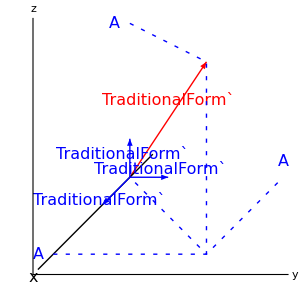

```mathematica
fontsize=16;Graphics[{Red,Arrow[{{0,0},{1,1.5}}],Text[Style["TraditionalForm`",fontsize],{0.5,1}], 
    Black,Line[{{0.3,0.3},{-1.2,-1.2}}],Text[Style[fBox["TraditionalForm`x"],fontsize],{-1.2,-1.2},{1,1}],
Blue,{ Dashing[{0.01,0.02}],Line[{{0,2},{1,1.5},{1,-1},{0,0}}],Line[{{-1,-1},{1,-1},{2,0}}]},
  Text[Style["A",fontsize],{-1.2,-1}],Text[Style["A",fontsize],{2,0.2}],Text[Style["A",fontsize],{-0.2,2}],
Arrow[{{0,0},{0.5,0}}],Text[Style["TraditionalForm`",fontsize],{0.4,0.1}],
Arrow[{{0,0},{0,0.5}}],Text[Style["TraditionalForm`",fontsize],{-0.1,0.3}],
Arrow[{{0,0},1/(√2){-0.5,-0.5}}],Text[Style["TraditionalForm`",16],{-0.4,-0.3}]},
Axes -> True ,Ticks -> None, AxesLabel -> {fBox["y"],fBox["z"]},

AxesStyle->fontsize,PlotRange -> Automatic,ImageSize->300,
AspectRatio->1]
```

In other coordinate systems — we will use polar in two dimensions and cylindrical and spherical in three dimansions —  we will have other unit vectors, and will generically write

A⃗ = A_1 OverHat[e_1] +  A_2 OverHat[e_2] +  A_3 OverHat[e_3]       ,      General coordinates.

If the unit vectors (ê)_i are orthogonal and normalized to unity (orthonormal), then

(ê)_i · (ê)_j = δ_ij  ,    where  δ_ij=Piecewise[{{1, i=j}, {0, i≠j}}]       ,    Kronecker delta ·

### Dot product

The scalar or dot product of two vectors A⃗ and B⃗ is given by

A⃗ · B⃗  = A B  cos θ  
                    = A_x B_x +  A_y B_y +  A_z B_z

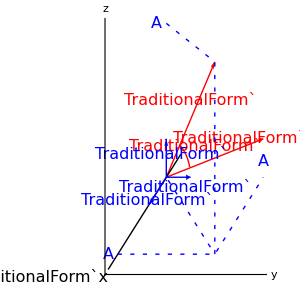

```mathematica
fontsize=16;
Graphics[{Red,Arrow[{{0,0},{1,1.5}}],Text[Style["TraditionalForm`",fontsize],{0.5,1}],
            Arrow[{{0,0},{2,0.5}}],Text[Style["TraditionalForm`",fontsize],{1.5,0.5}],Circle[{0,0},0.5,π {0.085,0.32}], Text[Style["TraditionalForm`",fontsize],{0.6,0.4}],
    Black,Line[{{0.3,0.3},{-1.2,-1.2}}],Text[Style["TraditionalForm`x",16],{-1.2,-1.2},{1,1}],
Blue,{ Dashing[{0.01,0.02}],Line[{{0,2},{1,1.5},{1,-1},{0,0}}],Line[{{-1,-1},{1,-1},{2,0}}]},
  Text[Style["A",fontsize],{-1.2,-1}],Text[Style["A",fontsize],{2,0.2}],Text[Style["A",fontsize],{-0.2,2}],
Arrow[{{0,0},{0.5,0}}],Text[Style["TraditionalForm`",fontsize],{0.4,-0.04},{0,1}],
Arrow[{{0,0},{0,0.5}}],Text[Style["TraditionalForm`",fontsize],{-0.1,0.3}],
Arrow[{{0,0},1/(√2){-0.5,-0.5}}],Text[Style["TraditionalForm`",16],{-0.4,-0.3}]},
Axes -> True ,Ticks -> None, AxesLabel -> {fBox["y"],fBox["z"]},
AxesStyle->16,PlotRange -> Automatic,ImageSize->300,
AspectRatio->1]
```

### Cross product

The vector or cross product of two vectors A⃗ and B⃗ is given by

A⃗ × B⃗  = A B  sin θ   OverHat[thumb]   
                       = | x̂ | ŷ | ẑ
A_x | A_y | A_z
B_x | B_y | B_z |
                    = x̂  ( A_y B_z -  A_z B_y )  +   ŷ  ( A_z B_x -  A_x B_z )  +  ẑ  ( A_x B_y -  A_y B_x )

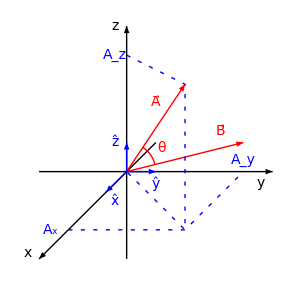

```mathematica
Graphics[{Map[Arrow[#]&,{{{-1.5,0},{2.5,0}},{{0,-1.5},{0,2.5}},{{0.5,0.5},{-1.5,-1.5}}}],Thick,Red,Arrow[{{0,0},{1,1.5}}], Arrow[{{0,0},{2,0.5}}],Circle[{0,0},0.5,π {0.085,0.32}],
Blue,{Dashing[{0.01,0.02}],Line[{{0,2},{1,1.5},{1,-1},{0,0}}],Line[{{-1,-1},{1,-1},{2,0}}]},
Arrow[{{0,0},{0.5,0}}],Arrow[{{0,0},{0,0.5}}],Arrow[{{0,0},1/(√2){-0.5,-0.5}}],Map[Text[Style[fBox[#_⟦1⟧],14,#_⟦2⟧],#_⟦3⟧]&,{{"TraditionalForm`x",Black,{-1.7,-1.4}},{"TraditionalForm`y",Black,{2.3,-0.2}},{"TraditionalForm`z",Black,{-0.2,2.5}},{"TraditionalForm`",Blue,{-0.2,-0.5}},{"TraditionalForm`",Blue,{0.5,-0.2}},{"TraditionalForm`",Blue,{-0.2,0.5}},{"A",Blue,{-1.3,-1}},{"A",Blue,{2,0.2}},{"A",Blue,{-0.2,2}},{"TraditionalForm`TraditionalForm`TraditionalForm`θ",Red,{0.6,0.4}},{"TraditionalForm`",Red,{0.5,1.2}},{"TraditionalForm`",Red,{1.6,0.7}}}]},
ImageSize->300]
```

### Levi-Civita symbol

Another way of writing  A⃗ × B⃗  is

C⃗ ≡  A⃗ × B⃗

where

C_i  = ∑_(j=1)^3 ∑_(k=1)^3  ϵ_ijk  A_j  B_k      .

Here, ϵ_ijk is the permutation symbol, or the Levi-Civita density, or Levi-Civita symbol, or the totally antisymmetric tensor of rank three.  It is defined as

ϵ_ijk  ≡Piecewise[{{0    ,, if any two of the i, j, k are equal}, {1    ,, if ijk is an even (or cyclic) permutation of 1,2,3}, {-1    ,, if ijk is an odd (noncyclic) permutation of 1,2,3}}]

─────────────────────────────────────────────────────────────────
* * * Lecture 2 — 22 August 2019 * * *

## Coordinate transformations

### 2-D rotation

Let the point P be located at (x_1,x_2}.  Let the primed coordinates x_1' and x_2' be new coordinates rotated by the angle θ.  Then, in the rotated coordinate frame, the coordinates of the point P are

x_1' = x_1 cos θ + x_2 sin θ  
  x_2' = - x_1 sin θ + x_2 cos θ          .

Mathematica knows about this transformation (We use -θ because Mathematica rotates the vector, and Thornton and Marion rotate the coordinates.):

```mathematica
MatrixForm[RotationTransform[-θ][{Subscript[x, 1],Subscript[x, 2]}]]
```

((√3 x_1)/2+x_2/2
-x_1/2+(√3 x_2)/2)

Here are two triangles with sides parallel to x_1' that add up to  x_1'=x_1 cosθ+x_2 sinθ  .

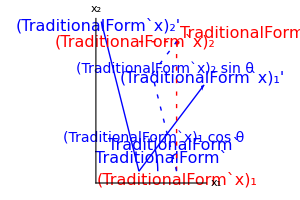

```mathematica
fontsize=16;
fontsize1=14;
θ=π/6;rt = RotationTransform[θ];mrt = RotationTransform[- θ];
Graphics[
{Red,Point[{1,1.5}],Text[Style["TraditionalForm`",fontsize],{1.1,1.6},{-1,0}],
    Blue,Arrow[{{0,0},rt[{2,0}]}],Text[Style["(TraditionalForm`x)_1'",fontsize],rt[{2,0.1}]],
               Arrow[{{0,0},rt[{0,2}]}],Text[Style["(TraditionalForm`x)_2'",fontsize],rt[{-0.1,2}]], Circle[{0,0},0.5, {0,θ}], Text[Style["TraditionalForm`",fontsize],{0.6,0.15}],
       Circle[{1,0},0.2,{π/2,π/2+θ}], Text[Style["TraditionalForm`",fontsize],{0.95,0.3}],
{ Dashing[{0.01,0.02}],Red,Line[{{0,1.5},{1,1.5},{1,0}}],Text[Style["(TraditionalForm`x)_1",fontsize],{1,-0.1}],Text[Style["(TraditionalForm`x)_2",fontsize],{-0.1,1.5}],
Blue,Line[{{1,0},RotationTransform[θ,{1,0}][{1,1.5Cos[θ]}],{1,1.5}}],
Text[Style["(TraditionalForm`x)_1 cos θ",fontsize1],{0.4,0.3},{0,-1},rt[{1,0}]],Text[Style["(TraditionalForm`x)_2 sin θ",fontsize1],{0.7,1.1},{0,-1},rt[{1,0}]]}},
Axes -> True ,Ticks -> None, AxesLabel -> {"x_1","x_2"},
AxesStyle->fontsize,PlotRange -> Automatic,ImageSize->300,
AspectRatio->Automatic]
```

Here are two triangles with sides parallel to x_2' that add up to  x_2'=- x_1 sin θ +x_2 cos θ.  Note that we have to subtract one from the other to get the coordinate x_2'.

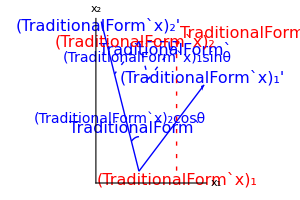

```mathematica
fontsize=16;
fontsize1=14;θ=π/6;rt = RotationTransform[θ];mrt = RotationTransform[- θ];
Graphics[
{Red,Point[{1,1.5}],Text[Style["TraditionalForm`",fontsize],{1.1,1.6},{-1,0}],
    Blue,Arrow[{{0,0},rt[{2,0}]}],Text[Style["(TraditionalForm`x)_1'",fontsize],rt[{2,0.1}]],
               Arrow[{{0,0},rt[{0,2}]}],Text[Style["(TraditionalForm`x)_2'",fontsize],rt[{-0.1,2}]], Circle[{0,0},0.4, {π/2,π/2+θ}], Text[Style["TraditionalForm`",fontsize],{-0.1,0.5}],
       Circle[{1,1.5},0.2,{π,π+θ}], Text[Style["TraditionalForm`",fontsize],{0.7,1.4}],
{ Dashing[{0.01,0.02}],Red,Line[{{0,1.5},{1,1.5},{1,0}}],Text[Style["(TraditionalForm`x)_1",fontsize],{1,-0.1}],
Text[Style["(TraditionalForm`x)_2",fontsize],{-0.1,1.5}],
Blue,Line[{{0,1.5},RotationTransform[θ,{0,1.5}][{-1.5Sin[θ],1.5}]}],            Line[{{1,1.5},{0,1.5},RotationTransform[θ,{0,1.5}][{0,1.5-Sin[θ]}],{1,1.5}}],
Text[Style["(TraditionalForm`x)_2cosθ",fontsize1],{-0.5,0.6},{0,0}, RotationTransform[θ+π][{0,1}]],
 Text[Style["(TraditionalForm`x)_1sinθ",fontsize1],{0.22,1.30},{0,0},RotationTransform[θ+π][{0,1}]]}},
Axes -> True ,Ticks -> None, AxesLabel -> {"x_1","x_2"},PlotRange -> Automatic,ImageSize->300,
AspectRatio->Automatic]
```

### A matrix form of the 2-D rotation using direction cosines

Now

sin θ = cos( θ - π/2) 
                       = cos(π/2- θ) = cos(x_1',x_2)     ,

where (x_1',x_2) is the angle between (x̂)_1' and (x̂)_2, and also

cos θ =  cos(x_1',x_1) =  cos(x_2',x_2)   ,
           
       - sin θ =  cos( θ + π/2)  = cos(x_2',x_1)    ,

as you can see from the graph below and the picture above.

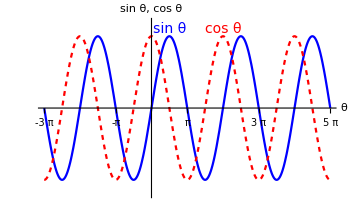

```mathematica
fontsize=14;
Plot[ {Sin[θ],Cos[θ]}, {θ,- 3π, 5π}, 
PlotStyle -> {Blue,{Dashing[{0.01,0.01}],Red}}, AxesLabel-> {"θ","sin θ, cos θ"},
AxesStyle->12,
Ticks -> {Range[ - 3π, 5π,π/2]},
PlotRange -> {-1.2,1.2},
Epilog -> {Text[Style["sin θ",{Blue,fontsize}], {π/2,1},{0,-1}],Text[Style["cos θ",{Red,fontsize}],{2π,1},{0,-1}]},
ImageSize -> 350  ]
```

Using these relations, we can write the equations relating the new coordinates of the point P to the old as

x_1' = λ_11  x_1 +λ_12  x_2  
	x_2' =λ_21  x_1 + λ_22  x_2      ,

with

λ_ij ≡ cos (x_i', x_j)    ,

which we call a "direction cosine".

Our equations now have the form of a matrix equation,

x̲' = UnderBar[λ̲] x̲        .

─────────────────────────────────────────────────────────────────
* * * Lecture 3 — 27 August 2019 * * *

### Why does a 2-D coordinate rotation work out this way?

Let the vector

R⃗ = x_1  (x̂)_1 + x_2  (x̂)_2

be a vector from the origin to the point P.

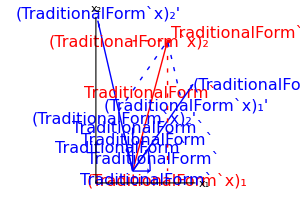

```mathematica
fontsize=16;
θ=π/6;
rt = RotationTransform[θ];
Graphics[
{Red,Point[{1,1.5}],
Text[Style["TraditionalForm`",fontsize],{1.1,1.6},{-1,0}],
Arrow[{{0,0},{1,1.5}}],
Text[Style["TraditionalForm`",fontsize],{0.5,0.9}],
    Blue,
Arrow[{{0,0},rt[{2,0}]}],Text[Style["(TraditionalForm`x)_1'",fontsize],rt[{2,0}],{-1.1,0}],
Text[Style["(TraditionalForm`x)_1'",fontsize],rt[{1.7,-0.1}]],
Arrow[{{0,0},rt[{0,2}]}],
Text[Style["(TraditionalForm`x)_2'",fontsize],rt[{0,2}],{0,-1}],Text[Style["(TraditionalForm`x)_2'",fontsize],rt[{-0.15,0.8}]],
 Circle[{0,0},0.5, {0,θ}], 
Text[Style["TraditionalForm`",fontsize],{0.6,0.15}],
{ Dashing[{0.01,0.02}],Red,Line[{{0,1.5},{1,1.5},{1,0}}],
Text[Style["(TraditionalForm`x)_1",fontsize],{1,-0.1}],
Text[Style["(TraditionalForm`x)_2",fontsize],{-0.1,1.5}],
Blue,Line[{rt[{0,1.5Cos[θ]- 1 Sin[θ]}],{1,1.5},rt[{1Cos[θ]+ 1.5 Sin[θ],0}]}]},
Arrow[{{0,0},{0.5,0}}],
Text[Style["TraditionalForm`",fontsize],{0.4,-0.1}],
Arrow[{{0,0},{0,0.5}}],
Text[Style["TraditionalForm`",fontsize],{0.15,0.5}],
Arrow[{{0,0},rt[{0.5,0}]}],
Text[Style["TraditionalForm`",fontsize],rt[{0.55,0.1}]],
Arrow[{{0,0},rt[{0,0.5}]}],
Text[Style["TraditionalForm`",fontsize],rt[{-0.15,0.4}]]},
Axes -> True ,Ticks -> None, AxesLabel -> {"x_1","x_2"},
AxesStyle->fontsize,PlotRange -> Automatic,ImageSize->300,
AspectRatio->Automatic]
```

Then,

x_1' = (x̂)_1' ·  R⃗ 
           = x_1 ((x̂)_1' ·  (x̂)_1) + x_2 ( (x̂)_1' ·  (x̂)_2 )

and

x_2' = (x̂)_1' ·  R⃗ 
           = x_1 ((x̂)_1' ·  (x̂)_1) + x_2 ( (x̂)_1' ·  (x̂)_2 )       .

### 3-D rotation

The way that the coordinates change under three-dimensional rotations can be worked out as above by simply writing

R⃗ = x_1  (x̂)_1 + x_2  (x̂)_2 + x_3  (x̂)_3    .

Then,

x_i' = (x̂)_i' ·  R⃗  = x_1 ((x̂)_i' ·  (x̂)_1) + x_2 ( (x̂)_i' ·  (x̂)_2 )  + x_3 ( (x̂)_i' ·  (x̂)_2 )  
                      =  ∑_(j=1)^3 ((x̂)_i' ·  (x̂)_j)   x_j                             .

We again set

λ_ij =  ((x̂)_i' ·  (x̂)_j)   ,

so that the new coordinates are

x_1' = λ_11   x_1  + λ_12  x_2  + λ_13  x_3 
	x_2' = λ_21   x_1  + λ_22  x_2  + λ_23  x_3 
	x_3' = λ_31   x_1  + λ_32  x_2  + λ_33  x_3

or

x_i' =  ∑_(j=1)^3 λ_ij  x_j

### Matrix notation

Set

UnderBar[λ̲]   ≡ (λ_11 | λ_12 | λ_13
λ_21 | λ_22 | λ_23
λ_31 |  λ_32 | λ_33)         ,

where you can  call the matrix UnderBar[λ̲] the transformation matrix, the rotation matrix, or the matrix of direction cosines.  Also define the vectors (now in the sense of column matrices)

x̲  ≡ (x_1
x_2
x_3)           and           x̲'  ≡ (x_1'
x_2'
x_3')        .

Then, matrix multiplication rules let us write

x_i' =  ∑_(j=1)^3 λ_ij  x_j

as

x̲' =  UnderBar[λ̲]   x̲       .

## Matrix operations

### m × n matrices

If

A   ≡ (A_11 | A_12 | ⋯ | A_(1n)
A_21 | A_22 | ⋯ | A_(2n)
⋮ | ⋮ |   | ⋮
A_m1 |  A_m2 | ⋯ | A_mn)^(n columns)   } m rows       ,

we call the matrix A an m × n matrix.  Thus, UnderBar[λ̲] is a 3 × 3 matrix, x̲  a 3 × 1 matrix, or a column matrix, or a column vector.  Its transpose

(x̲)^t ≡ [ x_1 | x_2 | x_3]

is a 1 × 3 matrix, or row vector.

### Matrix multiplication

If A and B are matrices, then

C = A B        matrix product

is defined as the matrix with elements

C_ij  =  ∑_(k=1)^3 A_ik  B_kj            .

Thus, to multiply matrices, you multiply rows by columns.

This is how we got

(x_1'
x_2'
x_3')  =   x̲' =  UnderBar[λ̲]   x̲    =  (λ_11 | λ_12 | λ_13
λ_21 | λ_22 | λ_23
λ_31 |  λ_32 | λ_33)   (x_1
x_2
x_3)   
                             =  (λ_11   x_1  + λ_12  x_2  + λ_13  x_3
λ_21   x_1  + λ_22  x_2  + λ_23  x_3 
 λ_31   x_1  + λ_32  x_2  + λ_33  x_3 )        .

We also wrote this as

x_i' =  ∑_(j=1)^3 λ_ij  x_j

by using a summation over the column index j .

### Addition and subtraction of matrices

The sum of two matrices is

A + B = (A_11 + B_11 | A_12 + B_12 | ⋯ | A_(1n) + B_(1n)
A_21 + B_21 | A_22 + B_22 | ⋯ | A_(2n) + B_(2n)
⋮ | ⋮ |   | ⋮
A_m1+ B_m1 |  A_m2 + B_m2 | ⋯ | A_mn+ B_mn)      .

To subtract, use a minus sign.

### Matrix multiplication is not commutative

A B ≠  B A  .

For an example, see Example 1.3 in the textbook.

### Transpose of a matrix

The transpose of the  m × n matrix A is the  n × m matrix

A^t   = ((A^t)_11 | (A^t)_12 | ⋯ | (A^t)_(1m)
(A^t)_21 | (A^t)_22 | ⋯ | (A^t)_(2m)
⋮ | ⋮ |   | ⋮
(A^t)_n1 |  (A^t)_n2 | ⋯ | (A^t)_mn) ≡ (A_11 | A_21 | ⋯ | A_m1
A_12 | A_22 | ⋯ | A_m2
⋮ | ⋮ |   | ⋮
A_(1n) |  A_(2n) | ⋯ | A_mn)   .

That is, you interchange rows and columns, so that the transpose of an m × n matrix is an n × m matrix.

### Identity matrix

The identity matrix is

𝟙  = (1 | 0 | ⋯ | 0
0 | 1 | ⋯ | 0
⋮ | ⋮ | ⋱ | ⋮
0 |  0 | ⋯ | 1)         .

Then,

A 𝟙 = 𝟙  A  = A   .

Also, the matrix elements of the identity are

𝕀_ij  =  δ_ij       .

### Inverse of a matrix

The inverse of the matrix A is the matrix that satisfies

A^-1  A  =  A  A^-1  = 𝟙      .

### Orthogonal matrices

A matrix A is called orthogonal if

A^t  =  A^-1        .

Then,

A   A^t  = A^t  A  = 𝟙   .

### Evaluation of determinants

The determinant of a 3 × 3 matrix is given by

det A  = | a_1 | b_1 | c_1
a_2 | b_2 | c_2
a_3 | b_3 | c_3 |  
            = a_1  | b_2 | c_2
b_3 | c_3 |  +  b_1  | c_2 | a_2
c_3 | a_3 | +  c_1  | a_2 | b_2
a_3 | b_3 |  
            =  a_1 ( b_2 c_3 - b_3 c_2 ) +  b_1 ( c_2 a_3 - c_3 a_2 ) +  c_1 ( a_2 b_3 - a_3 b_2 )   .

I have expanded about the first row.  Also, you can put the minus sign in the second term out in front of it.  You can expand about any row or column.

In general, the determinant is

det A = ∑_i (-1)^(i + 1) M_i1  = a_i C_i1   .

Here

M_ij is the "minor",which is the determinant formed 
			by omitting row i and column j.

C_ij  ≡  (-1)^(i + j) M_ij is the "cofactor".

This terminology is used to write the matrix elements of the inverse.  We have

[ A^-1 ]_ij  = C_ji/(| A |)     .

Note that the indices on the cofactor are reversed.  For the inverse to be defined, we must have det A ≠ 0.  If the determinant vanishes, we say that the matrix is singular, and it is not invertible.

─────────────────────────────────────────────────────────────────
* * * Lecture 4 — 29 August 2019 * * *

## Rotations as orthogonal transformations

Rotation matrices are orthogonal matrices, and the reason is that the coordinate systems are orthogonal.

To demonstrate this, consider any two vectors A⃗ and B⃗.

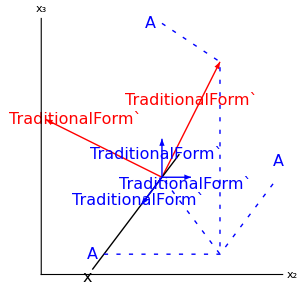

```mathematica
fontsize=16;
Graphics[{Red,Arrow[{{0,0},{1,1.5}}],
Text[Style["TraditionalForm`",fontsize],{0.5,1}],
            Arrow[{{0,0},{-2,0.75}}],
Text[Style["TraditionalForm`",fontsize],{-1.5,0.75}],
    Black,Line[{{0.3,0.3},{-1.2,-1.2}}],Text[Style["x",fontsize],{-1.2,-1.2},{1,1}],
Blue,{ Dashing[{0.01,0.02}],Line[{{0,2},{1,1.5},{1,-1},{0,0}}],Line[{{-1,-1},{1,-1},{2,0}}]},
  Text[Style["A",fontsize],{-1.2,-1}],
Text[Style["A",fontsize],{2,0.2}],
Text[Style["A",fontsize],{-0.2,2}],
Arrow[{{0,0},{0.5,0}}],
Text[Style["TraditionalForm`",fontsize],{0.4,-0.1}],
Arrow[{{0,0},{0,0.5}}],
Text[Style["TraditionalForm`",fontsize],{-0.1,0.3}],
Arrow[{{0,0},1/(√2){-0.5,-0.5}}],Text[Style["TraditionalForm`",fontsize],{-0.4,-0.3}]},
Axes -> True ,Ticks -> None, AxesLabel -> {"x_2","x_3"},
AxesStyle->fontsize,PlotRange -> Automatic,ImageSize->300,
AspectRatio->1]
```

Their scalar product is

A⃗ · B⃗ = ∑_j A_j B_j  
		        = ∑_j ( (x̂)_j · A⃗ )  ( (x̂)_j · B⃗)    .

Since the matrix elements of the rotation matrices are λ_ij = (x̂)_i' · (x̂)_j, that is, dot products of new and old unit vectors, let's choose A⃗ = (x̂)_i'  and B⃗ = (x̂)_k'.  This gives

A⃗ · B⃗ → (x̂)_i' · (x̂)_k'  = ∑_j ( (x̂)_j · (x̂)_i' )  ( (x̂)_j · (x̂)_k') 
                                                             = ∑_j (  (x̂)_i'  ·  (x̂)_j )  (  (x̂)_k' ·  (x̂)_j ) 
                                                             = ∑_j λ_ij  λ_kj                          .

We can put the right side in the form of a matrix product by substituting λ_kj = (λ^t)_jk.  Also, the new coordinates remain orthonormal, so the left side is

(x̂)_i' · (x̂)_k' = δ_ik.

Notice that this result arises because the unit vectors specifying the coordinates that we have chosen are orthogonal and normalized to unity.  If that were not true, we would not have the Kronecker delta appearing here, but something more complicated instead.

We end up with

∑_j λ_ij  (λ^t)_jk = δ_ik     .

Written as matrices, this says that

UnderBar[λ̲]   UnderBar[UnderBar[λ^t]]  =  UnderBar[𝟙]        ,

which shows that the rotation matrices are orthogonal matrices.

## Geometrical significance of rotation matrices

### Rotation matrices for a 90° rotation about x_3

Let's work out rotation matrices for a 90° rotation about x_3.  Here are the coordinates before rotation

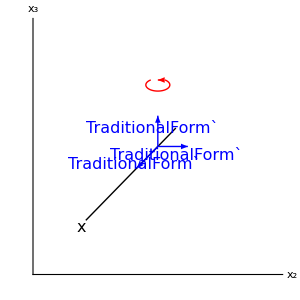

```mathematica
fontsize=16;
Graphics[{Black,Line[{{0.3,0.3},{-1.2,-1.2}}],Text[Style["x",fontsize],{-1.2,-1.2},{1,1}],
Blue,Arrow[{{0,0},{0.5,0}}],
Text[Style["TraditionalForm`",fontsize],{0.3,-0.15}],
Arrow[{{0,0},{0,0.5}}],
Text[Style["TraditionalForm`",fontsize],{-0.1,0.3}],
Arrow[{{0,0},1/(√2){-0.5,-0.5}}],
Text[Style["TraditionalForm`",fontsize],{-0.4,-0.3}], Red, Circle[{0,1},{0.2,0.1},{0.7π,2.3 π}],Arrow[{{0.1,1.08},{0,1.08}}]},
Axes -> True ,Ticks -> None, AxesLabel -> {"x_2","x_3"},
AxesStyle->16,
PlotRange -> {{-2,2},{-2,2}},ImageSize->300,
AspectRatio->1]
```

The appropriate rotation matrices

λ_ij  = (x̂)_i' · (x̂)_j = cos( x_i',x_j)

produce the new coordinates shown below.

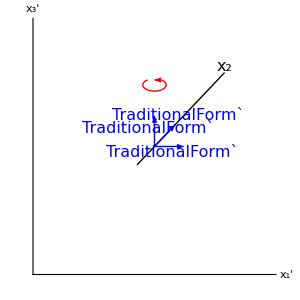

```mathematica
fontsize=16;
Graphics[{Black,Line[{{-0.3,-0.3},{1.2,1.2}}],Text[Style["x_2",fontsize],{1.2,1.3}],
Blue,Arrow[{{0,0},{0.5,0}}],
Text[Style["TraditionalForm`",fontsize],{0.3,-0.1}],
Arrow[{{0,0},{0,0.5}}],
Text[Style["TraditionalForm`",fontsize],{-0.1,0.3}],
Arrow[{{0,0},1/(√2){0.5,0.5}}],
Text[Style["TraditionalForm`",fontsize],{0.4,0.5}], Red, Circle[{0,1},{0.2,0.1},{0.7π,2.3 π}],Arrow[{{0.1,1.08},{0,1.08}}]},
Axes -> True ,Ticks -> None, AxesLabel -> {"x_1'","x_3'"},
AxesStyle->16,
PlotRange -> {{-2,2},{-2,2}},ImageSize->300,
AspectRatio->1]
```

Thus, for this rotation, which we will call "Rotation 1”, the rotation matrix is

Rotation matrix 1 ≡UnderBar[UnderBar[λ^(1)]]=((x̂)_1' · (x̂)_1  | (x̂)_1' · (x̂)_2  | (x̂)_1' · (x̂)_3 
(x̂)_2' · (x̂)_1  | (x̂)_2' · (x̂)_2  | (x̂)_2' · (x̂)_3 
(x̂)_3' · (x̂)_1  |  (x̂)_3' · (x̂)_2  | (x̂)_3' · (x̂)_3 )
                                                 =(0  | 1  | 0 
-1  | 0  | 0 
0  |  0  | 1 )                .

### Rotation matrices for a 90° rotation about x_1

Next, let's work out rotation matrices for a 90° rotation about x_1.  Here are he coordinates before rotation

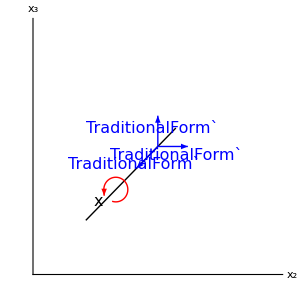

```mathematica
fontsize=16;Graphics[{Black,Line[{{0.3,0.3},{-1.2,-1.2}}],Text[Style["x",fontsize],{-1,-0.9}],
Blue,Arrow[{{0,0},{0.5,0}}],
Text[Style["TraditionalForm`",fontsize],{0.3,-0.15}],
Arrow[{{0,0},{0,0.5}}],
Text[Style["TraditionalForm`",fontsize],{-0.1,0.3}],
Arrow[{{0,0},1/(√2){-0.5,-0.5}}],
Text[Style["TraditionalForm`",fontsize],{-0.4,-0.3}], Red, Circle[0.7{-1,-1},{0.2,0.2},{-0.6π,1.1 π}],Arrow[{{-0.895,-0.75},{-0.895,-0.8}}]},
Axes -> True ,Ticks -> None, AxesLabel -> {"x_2","x_3"},
AxesStyle->16,
PlotRange -> {{-2,2},{-2,2}},ImageSize->300,
AspectRatio->1]
```

The appropriate rotation matrices

λ_ij  = (x̂)_i' · (x̂)_j = cos( x_i',x_j)

produce the new coordinates shown below.

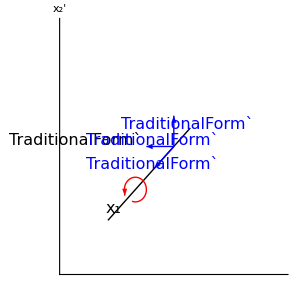

```mathematica
fontsize=16;Graphics[{Black,Line[{{0.3,0.3},{-1.2,-1.2}}],Text[Style["x_1",fontsize],{-1.1,-1.0}], 
Text[Style["TraditionalForm`",fontsize],{-1.8,0.1}], 
Blue,Arrow[{{0,0},{-0.5,0}}],
Text[Style["TraditionalForm`",fontsize],{-0.4,0.1}],
Arrow[{{0,0},{0,0.5}}],
Text[Style["TraditionalForm`",fontsize],{0.25,0.35}],
Arrow[{{0,0},1/(√2){-0.5,-0.5}}],Text[Style["TraditionalForm`",fontsize],{-0.4,-0.3}],
Red, Circle[0.7{-1,-1},{0.2,0.2},{-0.6π,1.1 π}],Arrow[{{-0.895,-0.75},{-0.895,-0.8}}]},
Axes -> True ,Ticks -> None, AxesLabel -> {None,"x_2'"},
AxesStyle->16,
PlotRange -> {{-2,2},{-2,2}},ImageSize->300,
AspectRatio->1]
```

Thus, for this rotation, which we will call "Rotation 2”, the rotation matrix is

Rotation matrix 2 ≡   UnderBar[UnderBar[λ^(2)]]=((x̂)_1' · (x̂)_1  | (x̂)_1' · (x̂)_2  | (x̂)_1' · (x̂)_3 
(x̂)_2' · (x̂)_1  | (x̂)_2' · (x̂)_2  | (x̂)_2' · (x̂)_3 
(x̂)_3' · (x̂)_1  |  (x̂)_3' · (x̂)_2  | (x̂)_3' · (x̂)_3 )=
		            =(1  | 0  | 0 
0 | 0  | 1 
0  |  -1  | 0 )                .

### Two rotations in succession

What is the result of performing rotation 1 and then following it by rotation 2?  Rotation 1 gives

x̲' = UnderBar[UnderBar[λ^(1)]]  x̲       .

Then, rotation 2 gives

x̲'' = UnderBar[UnderBar[λ^(2)]]  x̲' =  UnderBar[UnderBar[λ^(2)]]    UnderBar[UnderBar[λ^(1)]]   x̲   ≡  UnderBar[UnderBar[λ^(3)]]   x̲        .

The matrix representing rotation 3 is

UnderBar[UnderBar[λ^(3)]]  =  UnderBar[UnderBar[λ^(2)]]    UnderBar[UnderBar[λ^(1)]]  
	         =(1  | 0  | 0 
0 | 0  | 1 
0  |  -1  | 0 )  (0  | 1  | 0 
-1  | 0  | 0 
0  |  0  | 1 )   
	         = (0  | 1  | 0 
0 | 0  | 1 
1  |  0  | 0 )

```mathematica
{MatrixForm[({{1, 0, 0}, {0, 0, 1}, {0, -1, 0}}) . ({{0, 1, 0}, {-1, 0, 0}, {0, 0, 1}}) ],MatrixForm[ ({{0, 1, 0}, {-1, 0, 0}, {0, 0, 1}}) . ({{1, 0, 0}, {0, 0, 1}, {0, -1, 0}})]}
```

{(0 | 1 | 0
0 | 0 | 1
1 | 0 | 0),(0 | 0 | 1
-1 | 0 | 0
0 | -1 | 0)}

However, if we try the rotations in the opposite order,

UnderBar[UnderBar[λ^(2)]]    UnderBar[UnderBar[λ^(1)]]  
           = (0  | 1  | 0 
-1  | 0  | 0 
0  |  0  | 1 )  (1  | 0  | 0 
0 | 0  | 1 
0  |  -1  | 0 )   
           = (0  | 0  | 1 
-1 | 0  | 0 
0  |  -1  | 0 )    ≠ UnderBar[UnderBar[λ^(3)]]

UnderBar[UnderBar[λ^(2)]]    UnderBar[UnderBar[λ^(1)]] =
             =(0  | 1  | 0 
-1  | 0  | 0 
0  |  0  | 1 )  (1  | 0  | 0 
0 | 0  | 1 
0  |  -1  | 0 )
                 =(0  | 0  | 1 
-1 | 0  | 0 
0  |  -1  | 0 )    ≠ UnderBar[UnderBar[λ^(3)]]               .

we get a different result.  The two operations do not commute.  Try it with a book.

```mathematica
{λ1,λ2} = Map[RotationTransform[π/2,#] &, {{0,0,1},{1,0,0}}]
```

{TransformationFunction[(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)],TransformationFunction[(1 | 0 | 0 | 0
0 | 0 | -1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)]}

Here is the original unsymmetric cuboid.

```mathematica
fontsize=16;
Graphics3D[{Cuboid[{0.3,-2,-1},{-0.3,2,1}]},
Axes -> True, AxesLabel -> {"x_1","x_2","x_3"},
AxesStyle->fontsize,Ticks -> None,
ViewPoint -> {5,3,2}, ImageSize -> 150]
```

-Graphics3D-

```mathematica
g =Cuboid[{0.3,-2,-1},{-0.3,2,1}]
```

Cuboid[{0.3,-2,-1},{-0.3,2,1}]

Here is the result of applying rotation 1 to the original cuboid.

```mathematica
fontsize=16;
Graphics3D[GeometricTransformation[Cuboid[{0.3,-2,-1},{-0.3,2,1}],λ1],
Axes -> True, AxesLabel -> {"x_1","x_2","x_3"},
AxesStyle->fontsize,Ticks -> None,
ViewPoint -> {5,3,2}, ImageSize -> 120]
```

-Graphics3D-

Here is the result of applying rotation 2 to the original cuboid.

```mathematica
fontsize=16;Graphics3D[GeometricTransformation[Cuboid[{0.3,-2,-1},{-0.3,2,1}],λ2],
Axes -> True, AxesLabel -> {"x_1","x_2","x_3"},
AxesStyle->fontsize,Ticks -> None,
ViewPoint -> {5,3,2}, ImageSize -> 80]
```

-Graphics3D-

Here is the result of applying rotation 1 followed by rotation 2 to the original cuboid.

```mathematica
fontsize=16;Graphics3D[GeometricTransformation[Cuboid[{0.3,-2,-1},{-0.3,2,1}],Composition[λ2 , λ1]],
Axes -> True, AxesLabel -> {"x_1","x_2","x_3"},
AxesStyle->fontsize,Ticks -> None,
ViewPoint -> {5,3,2}, ImageSize -> 150]
```

-Graphics3D-

Here is the result of applying rotation 2 followed by rotation 1 to the original cuboid.

```mathematica
fontsize=16;Graphics3D[GeometricTransformation[Cuboid[{0.3,-2,-1},{-0.3,2,1}],Composition[λ1 , λ2]],
Axes -> True, AxesLabel -> {"x_1","x_2","x_3"},
AxesStyle->fontsize,Ticks -> None,
ViewPoint -> {5,3,2}, ImageSize -> 70]
```

-Graphics3D-

We see that these two rotations do not commute.

We can also use Rotate to rotate a graphics object by an angle about an axis.

```mathematica
fontsize=16;Graphics3D[Rotate[Cuboid[{0.3,-2,-1},{-0.3,2,1}],π/3, {0,0,1}],
Axes -> True, AxesLabel -> {"x_1","x_2","x_3"},
AxesStyle->fontsize,Ticks -> None,
ViewPoint -> {5,3,2}, ImageSize -> 150]
```

-Graphics3D-

## Additional properties of transformation matrices

### Rotation matrices can be regarded as either rotating the coordinates or the point P

Rotation matrices can be regarded as either rotating the coordinates or the point P.  We have described the rotation matrices as rotating the coordinates.  Another view, equally valid, regards them as rotating the point P.  In a practical situation, this point P is one of the points at which a particle of a physical system is located.  Thus, this latter point of view regards the axes as being left alone but the physical system of interest being rotated, like my basketball.  However, make up your mind as to which you want to do and stick to it.  Here, we have been regarding them as rotating coordinates.

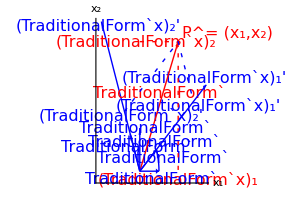

```mathematica
fontsize=16;
θ=π/6;
rt = RotationTransform[θ];
Graphics[
{Red,Point[{1,1.5}],
Text[Style["P^= (x_1,x_2) ",fontsize],{1.1,1.6},{-1,0}],
                     Arrow[{{0,0},{1,1.5}}],
Text[Style["TraditionalForm`",fontsize],{0.5,0.9}],
    Blue,Arrow[{{0,0},rt[{2,0}]}],
Text[Style["(TraditionalForm`x)_1'",fontsize],rt[{2,0.1}]],
Text[Style["(TraditionalForm`x)_1'",fontsize],rt[{1.7,-0.1}]],
               Arrow[{{0,0},rt[{0,2}]}],
Text[Style["(TraditionalForm`x)_2'",fontsize],rt[{-0.1,2}]],
Text[Style["(TraditionalForm`x)_2'",fontsize],rt[{-0.1,0.8}]],
 Circle[{0,0},0.5, {0,θ}], 
Text[Style["TraditionalForm`",fontsize],{0.6,0.15}],Arrow[{{0.45,0.21},{0.44,0.23}}],
{ Dashing[{0.01,0.02}],Red,Line[{{0,1.5},{1,1.5},{1,0}}],
Text[Style["(TraditionalForm`x)_1",fontsize],{1,-0.1}],
Text[Style["(TraditionalForm`x)_2",fontsize],{-0.1,1.5}],
Blue,Line[{rt[{0,1.5Cos[θ]- 1 Sin[θ]}],{1,1.5},rt[{1Cos[θ]+ 1.5 Sin[θ],0}]}]},
Arrow[{{0,0},{0.5,0}}],
Text[Style["TraditionalForm`",fontsize],{0.3,-0.1}],
Arrow[{{0,0},{0,0.5}}],
Text[Style["TraditionalForm`",fontsize],{0.15,0.5}],
Arrow[{{0,0},rt[{0.5,0}]}],
Text[Style["TraditionalForm`",fontsize],rt[{0.5,0.1}]],
Arrow[{{0,0},rt[{0,0.5}]}],
Text[Style["TraditionalForm`",fontsize],rt[{-0.15,0.4}]]},
Axes -> True ,Ticks -> None, AxesLabel -> {"x_1","x_2"},
AxesStyle->fontsize,PlotRange -> Automatic,ImageSize->300,
AspectRatio->Automatic]
```

To instead rotate the point P with the axes fixed, rotate the primed coordinates back to match the original unprimed ones.

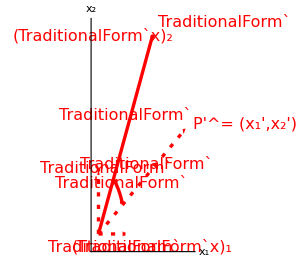

```mathematica
fontsize=16;
θ=π/6;
rt = RotationTransform[θ];
Graphics[
{Arrowheads[{0.05}],Thickness[0.008],
Red,Point[{1,1.5}],
Text[Style["TraditionalForm`",fontsize],{1.1,1.6},{-1,0}],
                     Arrow[{{0,0},{1,1.5}}],
Text[Style["TraditionalForm`",fontsize],{0.5,0.9}],
             Circle[{0,0},0.5, {0.32π-θ,.32π}], 
Text[Style["TraditionalForm`",fontsize],{0.43,0.38}],Arrow[{{0.425,0.25},{0.435,0.23}}],
 Dashing[{0.01,0.02}],
Text[Style["P'^= (x_1',x_2') ",fontsize], RotationTransform[-θ][{1.1,1.6}],{-1,0}],
                     Arrow[{{0,0}, RotationTransform[-θ][{1,1.5}]}],
Text[Style["TraditionalForm`",fontsize], RotationTransform[-θ][{0.5,0.9}]],
{ Dashing[{0.01,0.02}],Red,
Text[Style["(TraditionalForm`x)_1",fontsize],{1,-0.1}],
Text[Style["(TraditionalForm`x)_2",fontsize],{-0.1,1.5}]},
Arrow[{{0,0},{0.5,0}}],
Text[Style["TraditionalForm`",fontsize],{0.3,-0.1}],
Arrow[{{0,0},{0,0.5}}],
Text[Style["TraditionalForm`",fontsize],{0.15,0.5}]},
Axes -> True ,Ticks -> None, AxesLabel -> {"x_1","x_2"},
AxesStyle->fontsize,
PlotRange -> Automatic,ImageSize->300,
AspectRatio->Automatic]
```

Notice that the point P has rotated in the opposite sense.  The direction of rotation is opposite in the two points of view.  Coordinates go one way, the object the other.

─────────────────────────────────────────────────────────────────
* * * Lecture 5 — 3 September 2019 * * *

### The products of orthogonal matrices are orthogonal

The rule for the transpose of a product is

(A B)^t = B^t A^t.

The rotation matrices UnderBar[λ̲] are orthogonal, that is,

UnderBar[λ̲]  UnderBar[UnderBar[λ^t]] = UnderBar[λ̲]  UnderBar[UnderBar[λ^-1]]  =  𝟙  .

Now, if we write

UnderBar[UnderBar[λ^(3)]]  =  UnderBar[UnderBar[λ^(2)]]    UnderBar[UnderBar[λ^(1)]]    ,

we have

( UnderBar[UnderBar[λ^(3)]] )^t = ( UnderBar[UnderBar[λ^(1)]] )^t  ( UnderBar[UnderBar[λ^(2)]] )^t     .

This gives

UnderBar[UnderBar[λ^(3)]]    ( UnderBar[UnderBar[λ^(3)]] )^t   =  [   UnderBar[UnderBar[λ^(2)]]    UnderBar[UnderBar[λ^(1)]]   ]  [ ( UnderBar[UnderBar[λ^(1)]] )^t  ( UnderBar[UnderBar[λ^(2)]] )^t   ] 
                                         =     UnderBar[UnderBar[λ^(2)]]    UnderBar[UnderBar[λ^(1)]]    ( UnderBar[UnderBar[λ^(1)]] )^-1  ( UnderBar[UnderBar[λ^(2)]] )^-1   
                                         =     UnderBar[UnderBar[λ^(2)]]   𝟙  ( UnderBar[UnderBar[λ^(2)]] )^-1   
                                         =     UnderBar[UnderBar[λ^(2)]]   ( UnderBar[UnderBar[λ^(2)]] )^-1   = 𝟙   .

This shows that the product matrix UnderBar[UnderBar[λ^(3)]] is orthogonal.

### Inversion

An example of a transformation that is not a rotation is inversion.  Inversion reverses the direections of all three axes.  Here are the coordinates before inversion.

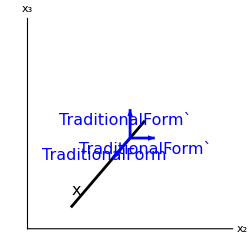

```mathematica
fontsize=16;Graphics[{Arrowheads[{0.05}],Thickness[0.008],Black,Line[{{0.3,0.3},{-1.2,-1.2}}],
Text[Style["x",fontsize],{-1.1,-0.9}],
Blue,Arrow[{{0,0},{0.5,0}}],
Text[Style["TraditionalForm`",fontsize],{0.3,-0.2}],
Arrow[{{0,0},{0,0.5}}],
Text[Style["TraditionalForm`",fontsize],{-0.1,0.3}],
Arrow[{{0,0},1/(√2){-0.5,-0.5}}],
Text[Style["TraditionalForm`",fontsize],{-0.45,-0.3}]},
Axes -> True ,Ticks -> None, AxesLabel -> {"x_2","x_3"},
AxesStyle->fontsize,PlotRange -> {{-2,2},{-1.5,2}},ImageSize->250,
AspectRatio->1]
```

Here are the new coordinates after inversion.

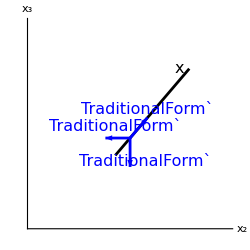

```mathematica
fontsize=16;Graphics[{Arrowheads[{0.05}],Thickness[0.008],
Black,Line[{{-0.3,-0.3},{1.2,1.2}}],
Text[Style["x",fontsize],{1,1.2}],
Blue,Arrow[{{0,0},{-0.5,0}}],
Text[Style["TraditionalForm`",fontsize],{-0.3,0.2}],
Arrow[{{0,0},{0,-0.5}}],
Text[Style["TraditionalForm`",fontsize],{0.3,-0.4}],
Arrow[{{0,0},1/(√2){0.5,0.5}}],
Text[Style["TraditionalForm`",fontsize],{0.35,0.5}]},
Axes -> True ,Ticks -> None, AxesLabel -> {"x_2","x_3"},
AxesStyle->fontsize,PlotRange -> {{-2,2},{-1.5,2}},ImageSize->250,
AspectRatio->1]
```

The matrix that represents inversion is

UnderBar[λ̲]  = (-1  | 0 | 0
0 | -1 | 0
0 |  0 | -1)  = ( - 1 ) 𝟙      .

### Determinants of transformation matrices

The determinants of rotation matrices are all + 1.  Sometimes theses matrices are called "proper rotations”.  However, if inversion is one step, the determinant is - 1.  "Improper rotations” include an inversion.

Here is a argument to show that the determinants of the matrices that represent proper rotations are + 1.  A rotation matrix has elements

λ_ij  = (x̂)_i' · (x̂)_j

where the primed coordinates are rotated relative to the unprimed ones.  Thus, a rotation is represented by the matrix

UnderBar[λ̲]   = ((x̂)_1' · (x̂)_1  | (x̂)_1' · (x̂)_2  | (x̂)_1' · (x̂)_3 
(x̂)_2' · (x̂)_1  | (x̂)_2' · (x̂)_2  | (x̂)_2' · (x̂)_3 
(x̂)_3' · (x̂)_1  |  (x̂)_3' · (x̂)_2  | (x̂)_3' · (x̂)_3 )     .

Now, the coordinates of a point change under this coordinate transformation, and the new coordinates are

(x_1' 
x_2' 
x_3' )  =  (λ_11  | λ_12  | λ_13 
λ_21  | λ_22  | λ_23 
λ_31 |  λ_32  | λ_33 )  (x_1 
x_2 
x_3 )  = (λ_11 x_1 + λ_12 x_2  + λ_13 x_3  
λ_21 x_1 + λ_22 x_2  + λ_23 x_3
λ_31 x_1 + λ_32 x_2  + λ_33 x_3)       .

We can regard the coordinate as specifying  the tip of a vector r⃗ that has its base at the origin.  Suppose that r⃗ = (x̂)_1.  Then we have

(x_1' 
x_2' 
x_3' )  =   (λ_11  | λ_12  | λ_13 
λ_21  | λ_22  | λ_23 
λ_31 |  λ_32  | λ_33 )  (1
0 
0 )  = (λ_11
λ_21
λ_31)  .

We get similar results for  r⃗ = (x̂)_2 and  r⃗ = (x̂)_3.   Thus, the λ_ij are the i th components of the original unit vector (x̂)_j in the new coordinate system.

Conversely, we may imagine that we rotate the original unit vectors as in Section 1.6.1 to get rotated unit vectors OverHat[x_i]'.  The expansion of these rotated unit vectors in terms of the unrotated ones is

(x̂)_i' = ∑_(j=1)^3 λ_ij   (x̂)_j     ,

because the λ_ij are the projections (i.e components) of the unit vector  (x̂)_i' along the original directions (x̂)_j.  Writing this out in matrix form gives

((x̂)_1' 
(x̂)_2' 
(x̂)_3' )  =  (λ_11  | λ_12  | λ_13 
λ_21  | λ_22  | λ_23 
λ_31 |  λ_32  | λ_33 )  ((x̂)_1 
(x̂)_2 
(x̂)_3 )     .

In homework problem 1.2 (Thornton and Marion, Fifth Edition, problem 1.11) we showed that the triple scalar product ( A⃗ × B⃗ ) · C⃗ can be written as

( A⃗ × B⃗ ) · C⃗ = | A_1 | A_2 | A_3
B_1 | B_2 | B_3
C_1 | C_2 | C_3 |    ,

where the A_i are the components of the vector A⃗ etc.  In addition, we showed that the triple scalar product ( A⃗ × B⃗ ) · C⃗ is the volume of the parallelopiped spanned by the three vectors.  This gives

( (x̂)_1' × (x̂)_2' ) · (x̂)_3' = | λ_11  | λ_12  | λ_13 
λ_21  | λ_22  | λ_23 
λ_31 |  λ_32  | λ_33  |  =  1    ,

because the three unit vectors form an orthonormal triad and do not change their lengths or relative angles on rotation.  They are orthgonal unit vectors.  The parallelopiped that they define is a cube of side one and volume unity.  Hence, the determinant of a (proper) rotation matrix is + 1.

Now we turn to improper rotations that involve an inversion as one step.  Inversion alone is represented by the matrix

UnderBar[UnderBar[λ^(inversion)]]  = (-1  | 0 | 0
0 | -1 | 0
0 |  0 | -1)  = ( - 1 ) 𝟙   ,

which clearly has determinant - 1.  A result for the determinant of a product that we have not proved (but it is true, See Arfken and Weber, Fifth Edition, Section 3.2, p. 169, where this is called the product theorem)  is that the determinant of a product is the product of the determinant,

det (A B) = (det A)  (det B).

Thus, a product of proper rotations with one inversion along the way has determinant (+1) (+1)  ⋯ (-1) ⋯ (+1) = -1.

## Definitions of a scalar and vector in terms of transformation properties

### Scalars

Quantities that remain invariant under a coordinate transformation are called scalars.  That is, if a scalar has value S before a coordinate transformation, and after transformation has value S', then it is a scalar if

S' = S       .

### Vectors

If a set of quantities { A_1, A_2, A_3} transform as

A_i' = ∑_(j=1)^3 λ_ij A_j       ,

where λ_ij are the matrix elements of a transformation matrix, under all coordinate transformations UnderBar[λ̲], than we say that the set  A_1, A_2, A_3} are the components of a vector A⃗.

There is a useful table of vector identities in Marion p. 28, but cite the equation number when you use one.  One of these days, you will have to prove these.  You may have proved some already, depending on what math courses you took.

## Differentiation of vectors by scalars

### Differentiation of scalars by scalars

Let ϕ(s) be a scalar function of a scalar variable s.  Since both s and ϕ(s) are invariant under a coordinate transformation x_i → x_i', we have s = s' and ϕ = ϕ'.  Thus,

(dϕ'(s' ))/(d s')  =  (dϕ( s ))/ds       ,

and this derivative is a scalar.

─────────────────────────────────────────────────────────────────
* * * Lecture 6 — 5 September 2019 * * *

### Differentiation of vectors by scalars

Let A⃗  =  A⃗(s) be a vector function of a scalar variable s.  Then, under a coordinate transformation x_i → x_i', the vector A⃗ changes according to

A_i'  = ∑_j λ_ij  A_j   .

If λ_ij is independent of s — and it always is in this course (e.g λ_ij independent of time) —  then

(dA_i'(s' ))/(d s')  = ∑_j λ_ij (dA_j( s ))/ds       .

This derivative is a vector.

Here is a picture.  We express the derivative as a limiting process

(d A⃗)/ds  =  lim_(Δs → 0)  (Δ A⃗)/Δs 
         =  lim_(Δs → 0)  (A⃗( s + Δs ) - A⃗( s ))/Δs       .

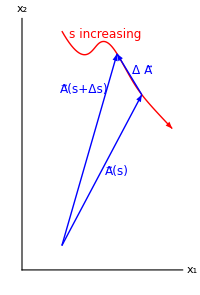

```mathematica
fontsize=12;curve={{0,5.5},{0.6,4.5},{1,5.5},{1.5,5.0},{2,4},{2.5,3.5},{3,3}};
curveFunc=BSplineFunction[curve];
curvepts=Map[curveFunc[#]&,Range[0,1,0.01]];
Graphics[{Arrowheads[{-0.002,-0.04,-0.002,-0.002,-0.002,-0.002,-0.04,-0.002}],
Thickness[0.005],
Red,Arrow[curvepts],
Text[Style[fBox["s increasing"],fontsize],{0.2,5.4},{-1,0}],
Arrowheads[{0.05}],
Blue,Arrow[{{0,0},curveFunc[0.5]}],Arrow[{{0,0},curveFunc[0.8]}],Arrow[{curveFunc[0.8],curveFunc[0.5]}],Text[Style[fBox["A⃗(s+Δs)"],fontsize],{0.6,4}],
Text[Style[fBox["A⃗(s)"],fontsize],{1.5,1.9}],
Text[Style[fBox["ΔA⃗"],fontsize],{1.9,4.5},{-1,0}]},Axes -> True,AxesLabel -> {"x_1","x_2"},
AxesStyle->fontsize,
PlotRange -> {{-1,3.2},{-0.5,5.7}}, Ticks -> None, ImageSize->200]
```

### Some relations that you can prove

If A⃗(s) and B⃗(s) are vectors, then

d/ds(A⃗+B⃗)=(d A⃗)/ds+(d B⃗)/ds    ,
 
          d/ds(A⃗·B⃗)=( (d A⃗)/ds )·B⃗ +A⃗·((d B⃗)/ds)     ,  
 
           d/ds( A⃗×  B⃗)=((d A⃗)/ds)×B⃗+A⃗×((d B⃗)/ds)    ,

and

d/ds(φ A⃗)=(dφ/ds) A⃗+φ ((d A⃗)/ds)    ,

where φ is a scalar.

## Velocity and acceleration

This is an example of differation by a scalar, time.

### Rectangular coordinates

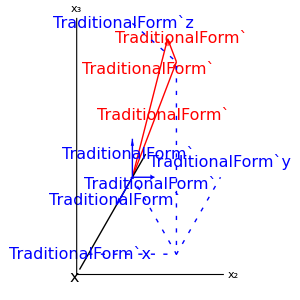

```mathematica
fontsize=16;
Graphics[{Red,
Arrow[{{0,0},{1,1.5}}],
Text[Style["TraditionalForm`",fontsize],{0.7,0.8}],
Arrow[{{0,0},{0.8,1.8}}],
Text[Style["TraditionalForm`",fontsize],{0.35,1.4}],
 Arrow[{{1,1.5},{0.8,1.8}}],
Text[Style["TraditionalForm`",fontsize],{1.1,1.8}],
    Black,Line[{{0.3,0.3},{-1.2,-1.2}}],Text[Style["x",fontsize],{-1.2,-1.2},{1,1}],
Blue,{ Dashing[{0.01,0.02}],Line[{{0,2},{1,1.5},{1,-1},{0,0}}],Line[{{-1,-1},{1,-1},{2,0}}]},
  Text[Style["TraditionalForm`x",fontsize],{-1.2,-1}],
Text[Style["TraditionalForm`y",fontsize],{2,0.2}],
Text[Style["TraditionalForm`z",fontsize],{-0.2,2}],
Arrow[{{0,0},{0.5,0}}],
Text[Style["TraditionalForm`",fontsize],{0.4,-0.1}],
Arrow[{{0,0},{0,0.5}}],
Text[Style["TraditionalForm`",fontsize],{-0.1,0.3}],
Arrow[{{0,0},1/(√2){-0.5,-0.5}}],
Text[Style["TraditionalForm`",fontsize],{-0.4,-0.3}]},
Axes -> True ,Ticks -> None, AxesLabel -> {"x_2","x_3"},
AxesStyle->fontsize,
PlotRange -> Automatic,ImageSize->300,
AspectRatio->1]
```

The position is

r⃗ = ∑_i x_i (ê)_i      .

An infinitesimal change in position is

d r⃗ = ∑_i d x_i  (ê)_i        .

The velocity is

v⃗ = OverDot[r⃗] = ∑_i (ẋ)_i (ê)_i + ∑_i x_i OverDot[ê]_i  .

In rectangular coordinates OverDot[ê]_i = 0  (but not in other systems), and so

v⃗ = ∑_i (ẋ)_i (ê)_i     .       Rectangular Coordinates

The acceleration is

a⃗ = OverDot[v⃗] =  OverDoubleDot[r⃗]  = ∑_i (ẍ)_i (ê)_i + ∑_i (ẋ)_i OverDot[ê]_i  .

In rectangular coordinates OverDot[ê]_i = 0, and so

a⃗ = ∑_i ((ẍ)_i)_i (ê)_i     .         Rectangular Coordinates

### Plane polar coordinates r, θ

Here, the unit vectors change direction as the position changes.  The position is

r⃗ =  r  (ê)_r      .

An infinitesimal change in position is given by

d r⃗ =   (ê)_r dr  +  (ê)_θ r dθ       .

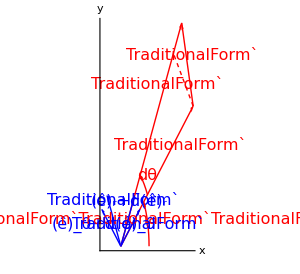

```mathematica
fontsize=16;
{θ1,θ2}={0.2,0.3}π;Graphics[{ Red,Arrow[{{0,0},1.9{Cos[θ1],Sin[θ1]}}],Text[Style["TraditionalForm`",fontsize],1.5{Cos[0.9 θ1],Sin[0.9 θ1]}],
            Arrow[{{0,0},2.2{Cos[θ2],Sin[θ2]}}],Text[Style["TraditionalForm`",fontsize],1.5{Cos[1.1 θ2],Sin[1.1 θ2]}],
         Arrow[{1.9{Cos[θ1],Sin[θ1]},2.2{Cos[θ2],Sin[θ2]}}],Text[Style["TraditionalForm`",fontsize],2.15{Cos[(θ1+θ2)/2],Sin[(θ1+θ2)/2]}],
{Dashing[{0.01,0.01}],Line[{1.9{Cos[θ1],Sin[θ1]},1.9{Cos[θ2],Sin[θ2]}}]},
Circle[{0,0},0.6,{0,θ1}],Arrow[{0.6{Cos[0.99θ1],Sin[0.99θ1]},0.6{Cos[θ1],Sin[θ1]}}],Text[Style["TraditionalForm`TraditionalForm`TraditionalForm`θ\ ",fontsize],0.7{Cos[θ1/2],Sin[θ1/2]}],
Circle[{0,0},0.7,{θ1,θ2}],Arrow[{0.7{Cos[0.99θ2],Sin[0.99θ2]},0.7{Cos[θ2],Sin[θ2]}}],Text[Style[fBox["dTraditionalForm`TraditionalForm`TraditionalForm`θ"],fontsize],0.8{Cos[(θ1+θ2)/2],Sin[(θ1+θ2)/2]}],
Blue,Arrow[{{0,0},0.5{Cos[θ1],Sin[θ1]}}],Text[Style["TraditionalForm`",fontsize],0.4{Cos[0.7 θ1],Sin[0.7θ1]}],
Arrow[{{0,0},0.5{Cos[θ2],Sin[θ2]}}],Text[Style[fBox["TraditionalForm`+dTraditionalForm`"],fontsize],0.4{Cos[1.2 θ2],Sin[1.2 θ2]},{0,0},{Cos[θ2],Sin[ θ2]}],
Arrow[{{0,0},0.5{Cos[θ1+π/2],Sin[θ1+π/2]}}],Text[Style["TraditionalForm`",fontsize],0.4{Cos[0.7 θ1+π/2],Sin[0.7θ1+π/2]}],
Arrow[{{0,0},0.5{Cos[θ2+π/2],Sin[θ2+π/2]}}],Text[Style[fBox["TraditionalForm`+dTraditionalForm`"],fontsize],0.4{Cos[1.2 θ2+π/2],Sin[1.2 θ2+π/2]},{0,0},{Cos[θ2-π/2],Sin[ θ2-π/2]}]},
Axes -> True ,Ticks -> None, AxesLabel -> {fBox["x"],fBox["y"]},
AxesStyle->fontsize,PlotRange -> Automatic,ImageSize->300,
AspectRatio->Automatic]
```

We need the change in the unit vectors as r changes by dr and θ changes by dθ.

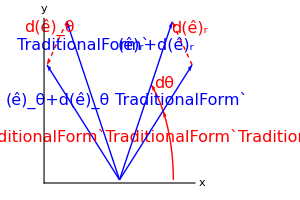

```mathematica
fontsize=16;
{θ1,θ2}={0.2,0.3}π;Graphics[{ Red,{Dashing[{0.01,0.01}],
          Arrow[{0.5{Cos[θ1],Sin[θ1]},0.5{Cos[θ2],Sin[θ2]}}],Text[Style[fBox["dTraditionalForm`"],fontsize],0.55{Cos[(θ1+θ2)/2],Sin[(θ1+θ2)/2]}],
            Arrow[{0.5{Cos[θ1+π/2],Sin[θ1+π/2]},0.5{Cos[θ2+π/2],Sin[θ2+π/2]}}],Text[Style[fBox["dTraditionalForm`"],fontsize],0.55{Cos[(θ1+θ2)/2+π/2],Sin[(θ1+θ2)/2+π/2]}]},
Circle[{0,0},0.3,{0,θ1}],Arrow[{0.3{Cos[0.99θ1],Sin[0.99θ1]},0.3{Cos[θ1],Sin[θ1]}}],Text[Style["TraditionalForm`TraditionalForm`TraditionalForm`θ\ ",fontsize],0.35{Cos[θ1/2],Sin[θ1/2]}],
Circle[{0,0},0.3,{θ1,θ2}],Arrow[{0.3{Cos[0.99θ2],Sin[0.99θ2]},0.3{Cos[θ2],Sin[θ2]}}],Text[Style[fBox["dTraditionalForm`TraditionalForm`TraditionalForm`θ"],fontsize],0.35{Cos[(θ1+θ2)/2],Sin[(θ1+θ2)/2]}],
Blue,Arrow[{{0,0},0.5{Cos[θ1],Sin[θ1]}}],Text[Style["TraditionalForm`",fontsize],0.4{Cos[0.85 θ1],Sin[0.85θ1]}],
Arrow[{{0,0},0.5{Cos[θ2],Sin[θ2]}}],Text[Style[fBox["TraditionalForm`+dTraditionalForm`"],fontsize],0.4{Cos[1.1 θ2],Sin[1.1 θ2]},{0,0},{Cos[θ2],Sin[ θ2]}],
Arrow[{{0,0},0.5{Cos[θ1+π/2],Sin[θ1+π/2]}}],Text[Style["TraditionalForm`",fontsize],0.4{Cos[0.85 θ1+π/2],Sin[0.85θ1+π/2]}],
Arrow[{{0,0},0.5{Cos[θ2+π/2],Sin[θ2+π/2]}}],Text[Style[fBox["TraditionalForm`+dTraditionalForm`"],fontsize],0.4{Cos[1.1 θ2+π/2],Sin[1.1 θ2+π/2]},{0,0},{Cos[θ2-π/2],Sin[ θ2-π/2]}]},
Axes -> True ,Ticks -> None, AxesLabel -> {fBox["x"],fBox["y"]},
AxesStyle->fontsize,
PlotRange -> Automatic,ImageSize->300,
AspectRatio->Automatic]
```

From the figure, we see that, since the unit vectors have length unity, the arc lengths of the red dashed arrows are both dθ, and they are

d(ê)_r = (ê)_θ dθ  
   d(ê)_θ = -  (ê)_r dθ        .

Thus, if the angular speed is dθ/dt = θ̇, the rates of change of the unit vectors are

OverDot[(ê)_r] = (ê)_θ  θ̇  
 OverDot[(ê)_θ] = -  (ê)_r   θ̇        .

Differentiating

r⃗  = r  (ê)_r

shows that the velocity is

v⃗ = OverDot[r⃗] = ṙ  (ê)_r +  r  OverDot[ê]_r  ,

which is

v⃗  = ṙ  (ê)_r +  r  θ̇ (ê)_θ     .

The velocity has both radial and tangential components.

The acceleration is

a⃗ = OverDot[v⃗] =  OverDoubleDot[r⃗]  
              =  r̈  (ê)_r  +  ṙ  OverDot[(ê)_r]  +  ṙ  θ̇ (ê)_θ  +   r  θ̈   (ê)_θ  +  r  θ̇ OverDot[(ê)_θ] 
              =  r̈  (ê)_r  +  ṙ  θ̇  (ê)_θ  +  ṙ  θ̇ (ê)_θ  +   r  θ̈   (ê)_θ  -  r  (θ̇)^2   (ê)_r 
              = (  r̈   -   r  (θ̇)^2 )  (ê)_r + ( r  θ̈   + 2  ṙ  θ̇  )  (ê)_θ     .

The second term of the radial component is the famous centripetal acceleration v_tangential^2/r.

─────────────────────────────────────────────────────────────────
* * * Lecture 7 — 10 September 2019 * * *

### Cylindrical coordinates r, ϕ, z

Here, the unit vectors change direction as the position changes.  The position is

r⃗ =  r  (ê)_r + z  (ê)_z     .

You can denote the coordinate r by  r_⊥ if you like.  An infinitesimal change in position is given by

d r⃗ =   (ê)_r dr  +  (ê)_ϕ  r dϕ  +   (ê)_z  dz       .

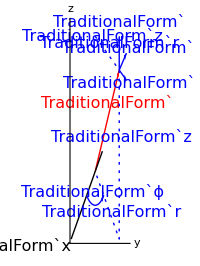

```mathematica
fontsize=16;
Graphics[{Red,
Arrow[{{0,0},{1,1.5}}],
Text[Style["TraditionalForm`",fontsize],{0.5,1}], 
    Black,Line[{{0.3,0.3},{-1,-1}}],
Text[Style["TraditionalForm`x",fontsize],{-1,-1},{1,1}],
Blue,{ Dashing[{0.01,0.02}],Line[{{0,2},{1,1.5},{1,-1},{0,0}}]},
Text[Style["TraditionalForm`z",fontsize,Background -> White],{1.1,0.5}],
Text[Style["TraditionalForm`r",fontsize,Background -> White],{0.7,-0.6}],
Text[Style["TraditionalForm`z",fontsize],{-0.1,2}],
Text[Style["TraditionalForm`r",fontsize],{0.6,1.9}],
Text[Style["TraditionalForm`ϕ",fontsize],{-0.1,-0.3}],Circle[{0,0},0.5,π {1.25,1.75}],
Arrow[{0.5{Cos[1.74π],Sin[1.74π]},0.5{Cos[1.75π],Sin[1.75π]}}],
Arrow[{{1,1.5},{1.3,1.35}}],
Text[Style["TraditionalForm`",fontsize],{1.4,1.3}],
Arrow[{{1,1.5},{1,2}}],
Text[Style["TraditionalForm`",fontsize],{1,2.2}],
Arrow[{{1,1.5},{1.3,1.75}}],
Text[Style["TraditionalForm`",fontsize],{1.37,1.82}]},
Axes -> True ,Ticks -> None, AxesLabel -> {fBox["y"],fBox["z"]},
AxesStyle->fontsize,PlotRange -> Automatic,ImageSize->200,
AspectRatio->Automatic]
```

Then, the velocity is

v⃗ = OverDot[r⃗] = ṙ  (ê)_r +  r  OverDot[ê]_r +  ż  (ê)_z +  z  OverDot[ê]_z  ,

with the rates of change of the unit vectors given by

OverDot[(ê)_r] = (ê)_ϕ ϕ̇  
 OverDot[(ê)_ϕ] = -  (ê)_r ϕ̇ 
  OverDot[(ê)_z] = 0

as you can see from the two-dimensional figure below.

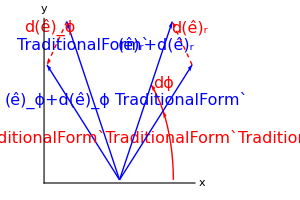

```mathematica
fontsize=16;
{θ1,θ2}={0.2,0.3}π;
Graphics[{Red,{Dashing[{0.01,0.01}],
          Arrow[{0.5{Cos[θ1],Sin[θ1]},0.5{Cos[θ2],Sin[θ2]}}],Text[Style[fBox["dTraditionalForm`"],fontsize],0.55{Cos[(θ1+θ2)/2],Sin[(θ1+θ2)/2]}],
            Arrow[{0.5{Cos[θ1+π/2],Sin[θ1+π/2]},0.5{Cos[θ2+π/2],Sin[θ2+π/2]}}],Text[Style[fBox["dTraditionalForm`"],fontsize],0.55{Cos[(θ1+θ2)/2+π/2],Sin[(θ1+θ2)/2+π/2]}]},
Circle[{0,0},0.3,{0,θ1}],Arrow[{0.3{Cos[0.99θ1],Sin[0.99θ1]},0.3{Cos[θ1],Sin[θ1]}}],Text[Style["TraditionalForm`TraditionalForm`TraditionalForm`ϕ\ ",fontsize],0.35{Cos[θ1/2],Sin[θ1/2]}],
Circle[{0,0},0.3,{θ1,θ2}],Arrow[{0.3{Cos[0.99θ2],Sin[0.99θ2]},0.3{Cos[θ2],Sin[θ2]}}],Text[Style[fBox["dTraditionalForm`TraditionalForm`TraditionalForm`ϕ"],fontsize],0.35{Cos[(θ1+θ2)/2],Sin[(θ1+θ2)/2]}],
Blue,Arrow[{{0,0},0.5{Cos[θ1],Sin[θ1]}}],Text[Style["TraditionalForm`",fontsize],0.4{Cos[0.85 θ1],Sin[0.85θ1]}],
Arrow[{{0,0},0.5{Cos[θ2],Sin[θ2]}}],Text[Style[fBox["TraditionalForm`+dTraditionalForm`"],fontsize],0.4{Cos[1.1 θ2],Sin[1.1 θ2]},{0,0},{Cos[θ2],Sin[ θ2]}],
Arrow[{{0,0},0.5{Cos[θ1+π/2],Sin[θ1+π/2]}}],Text[Style["TraditionalForm`",fontsize],0.4{Cos[0.85 θ1+π/2],Sin[0.85θ1+π/2]}],
Arrow[{{0,0},0.5{Cos[θ2+π/2],Sin[θ2+π/2]}}],Text[Style[fBox["TraditionalForm`+dTraditionalForm`"],fontsize],0.4{Cos[1.1 θ2+π/2],Sin[1.1 θ2+π/2]},{0,0},{Cos[θ2-π/2],Sin[ θ2-π/2]}]},
Axes -> True ,Ticks -> None, AxesLabel -> {fBox["x"],fBox["y"]},
AxesStyle->fontsize,PlotRange -> Automatic,ImageSize->300,
AspectRatio->Automatic]
```

To get these relations systematically, we can use the chain rule

d(ê)_r = ( (∂(ê)_r)/(∂r) ) dr +  ( (∂(ê)_r)/(∂ϕ) ) dϕ +  ( (∂(ê)_r)/(∂z) ) dz 
         =  0 +  ( (∂(ê)_r)/(∂ϕ) ) dϕ +  0 =  (ê)_ϕ  dϕ     ,

and so on.

Then, the velocity becomes

v⃗ = OverDot[r⃗] = ṙ  (ê)_r +  r  OverDot[ê]_r +  ż  (ê)_z +  z  OverDot[ê]_z 
         = ṙ  (ê)_r +  r  (  (ê)_ϕ  ϕ̇   ) +  ż  (ê)_z +  z  ( 0 )

or

v⃗ = ṙ  (ê)_r +  r  ϕ̇   (ê)_ϕ +  ż  (ê)_z      .

The acceleration is

a⃗ =  OverDoubleDot[r⃗]  =  r̈  (ê)_r  +  ṙ  OverDot[(ê)_r]  +  ṙ  ϕ̇ (ê)_ϕ  +   r  ϕ̈   (ê)_ϕ  +  r  ϕ̇ OverDot[(ê)_ϕ]  +  z̈  (ê)_z  +  ż OverDot[(ê)_z]
     =  r̈  (ê)_r  +  ṙ ( ϕ̇  (ê)_ϕ ) +  ṙ  ϕ̇ (ê)_ϕ  +   r  ϕ̈   (ê)_ϕ  -  r  (ϕ̇)^2   (ê)_r +  z̈  (ê)_z + 0     .

This is

a⃗ =  OverDoubleDot[r⃗]  = (  r̈   -   r  (ϕ̇)^2 )  (ê)_r + ( r  ϕ̈   + 2  ṙ  ϕ̇  )  (ê)_ϕ  +  z̈  (ê)_z

### Spherical coordinates r,θ, ϕ

You are doing this for homework (Assignment 2, homework problem 2.1).  I will not do the derivations here, but I’ll give you the pictures you will need.  You can copy and paste these into your homeowork, but you have to include detailed English explanations of what each picture is showing.  The first picture shows the position vector, spherical coordinate angles, and spherical coordinate unit vectors.

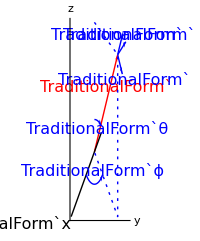

```mathematica
fontsize=16;
Graphics[{Red,Arrow[{{0,0},{1,1.5}}],
Text[Style["TraditionalForm`",fontsize],{0.5,1}], 
    Black,Line[{{0.3,0.3},{-1,-1}}],
Text[Style["TraditionalForm`x",fontsize],{-1,-1},{1,1}],
Blue,{ Dashing[{0.01,0.02}],Line[{{0,2},{1,1.5},{1,-1},{0,0}}]},
Text[Style["TraditionalForm`θ",fontsize],{0.1,0.35}],
Text[Style["TraditionalForm`ϕ",fontsize],{-0.1,-0.3}],
Circle[{0,0},0.5,π {1.25,1.75}],Arrow[{0.5{Cos[1.74π],Sin[1.74π]},0.5{Cos[1.75π],Sin[1.75π]}}],
Circle[{0,0},0.5,π {0.3,0.5}],Arrow[{0.5{Cos[0.31π],Sin[0.31π]},0.5{Cos[0.3π],Sin[0.3π]}}],
Arrow[{{1,1.5},{1.2,1.2}}],
Text[Style["TraditionalForm`",fontsize],{1.3,1.1}],
Arrow[{{1,1.5},{1.22,1.83}}],
Text[Style["TraditionalForm`",fontsize],{1,1.8}],
Arrow[{{1,1.5},{1.35,1.7}}],
Text[Style["TraditionalForm`",fontsize],{1.48,1.8}]},
Axes -> True ,Ticks -> None, AxesLabel -> {fBox["y"],fBox["z"]},
AxesStyle->fontsize,
PlotRange -> Automatic,ImageSize->200,
AspectRatio->Automatic]
```

You have to use the chain rule to get expressions for OverDot[(ê)_r], OverDot[(ê)_θ], and OverDot[(ê)_ϕ].

To see what happens to (ê)_r,  (ê)_θ and (ê)_ϕ when θ changes, draw a picture in the plane containing r⃗ and ẑ.  This gives us  (∂(ê)_r)/(∂θ), (∂(ê)_θ)/(∂θ), and (∂(ê)_ϕ)/(∂θ).

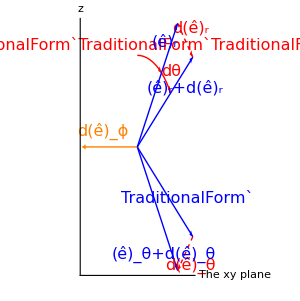

```mathematica
fontsize=16;{θ1,θ2}={0.2,0.3}π;Graphics[{ Red,{Dashing[{0.01,0.01}],
          Arrow[{0.5{Cos[θ2],Sin[θ2]},0.5{Cos[θ1],Sin[θ1]}}],Text[Style[fBox["dTraditionalForm`"],fontsize],0.55{Cos[(θ1+θ2)/2],Sin[(θ1+θ2)/2]}],
            Arrow[{0.5{Cos[θ2-π/2],Sin[θ2-π/2]},0.5{Cos[θ1-π/2],Sin[θ1-π/2]}}],Text[Style[fBox["dTraditionalForm`"],fontsize],0.55{Cos[(θ1+θ2)/2-π/2],Sin[(θ1+θ2)/2-π/2]}]},
Circle[{0,0},0.3,{θ2,π/2}],Arrow[{0.3{Cos[1.01θ2],Sin[1.01θ2]},0.3{Cos[θ2],Sin[θ2]}}],Text[Style["TraditionalForm`TraditionalForm`TraditionalForm`θ\ ",fontsize],0.35{Cos[(π-θ1)/2],Sin[(π-θ1)/2]}],
Circle[{0,0},0.3,{θ1,θ2}],Arrow[{0.3{Cos[1.01θ1],Sin[1.01θ1]},0.3{Cos[θ1],Sin[θ1]}}],Text[Style[fBox["dTraditionalForm`TraditionalForm`TraditionalForm`θ"],fontsize],0.35{Cos[(θ1+θ2)/2],Sin[(θ1+θ2)/2]}],
Blue,Arrow[{{0,0},0.5{Cos[θ1],Sin[θ1]}}],Text[Style[fBox["TraditionalForm`+dTraditionalForm`"],fontsize],0.4{Cos[0.8 θ1],Sin[0.8θ1]},{0,0},{Cos[θ1],Sin[θ1]}],
Arrow[{{0,0},0.5{Cos[θ2],Sin[θ2]}}],Text[Style[fBox["TraditionalForm`"],fontsize],0.4{Cos[1.1 θ2],Sin[1.1 θ2]}],
Arrow[{{0,0},0.5{Cos[θ2-π/2],Sin[θ2-π/2]}}],Text[Style["TraditionalForm`",fontsize],0.4{Cos[1.2θ2-π/2],Sin[1.2θ2-π/2]}],
Arrow[{{0,0},0.5{Cos[θ1-π/2],Sin[θ1-π/2]}}],Text[Style[fBox["TraditionalForm`+dTraditionalForm`"],fontsize],0.4{Cos[0.8 θ1-π/2],Sin[0.8 θ1-π/2]},{0,0},{Cos[θ1-π/2],Sin[ θ1-π/2]}],
Orange,Thick,Arrow[{{0,0},{-0.4,0}}],Text[Style[fBox["dTraditionalForm`"],fontsize],{-0.25,0.05}]},
Axes -> True ,Ticks -> None, AxesLabel -> {fBox["The xy plane"],fBox["z"]},
AxesStyle->fontsize,
PlotRange -> Automatic,ImageSize->300,
AspectRatio->Automatic]
```

Draw projection of (ê)_r on the x–y  plane, and explain what this shows.

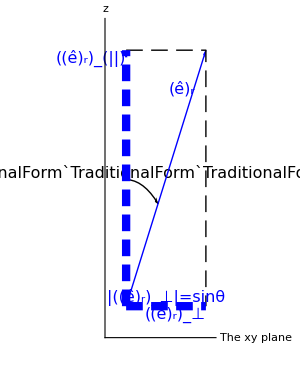

```mathematica
fontsize=16;
{θ1,θ2}={0.2,0.3}π;
ercoord=0.5{Cos[θ2],Sin[θ2]};
Graphics[{ Arrowheads[{0.08}],
Circle[{0,0},0.2,{θ2,π/2}],Arrow[{0.2{Cos[1.01θ2],Sin[1.01θ2]},0.2{Cos[θ2],Sin[θ2]}}],Text[Style["TraditionalForm`TraditionalForm`TraditionalForm`θ\ ",fontsize],0.22{Cos[(π-θ1)/2],Sin[(π-θ1)/2]}],
Blue,
Arrow[{{0,0},ercoord}],Text[Style[fBox["TraditionalForm`"],fontsize],0.4{Cos[1.1 θ2],Sin[1.1 θ2]}],
Black,Dashing[{0.04,0.02}],
Line[{{0,ercoord_⟦2⟧},ercoord,{ercoord_⟦1⟧,0}}],
Blue,Thickness[0.02],
Arrow[{{0,0},{ercoord_⟦1⟧,0}}],
Text[Style[fBox["(TraditionalForm`)_⊥"],fontsize],{ercoord_⟦1⟧,0},{1,1.2}],
Text[Style[fBox["|(TraditionalForm`)_⊥|=sinθ"],fontsize],0.5{ercoord_⟦1⟧,0},{0,-1.3}],
Arrow[{{0,0},{0,ercoord_⟦2⟧}}],
Text[Style[fBox["(TraditionalForm`)_(||)"],fontsize],{0,ercoord_⟦2⟧},{1.3,1}]},
Axes -> True ,Ticks -> None, AxesLabel -> {fBox["The xy plane"],fBox["z"]},
AxesStyle->fontsize,
PlotRange -> {{-0.07,1.1 ercoord_⟦1⟧},{-0.04,1.1 ercoord_⟦2⟧}},ImageSize->300,
AspectRatio->Automatic]
```

When ϕ changes, draw a picture in the x-y plane, to see how ((ê)_r)_(||), ((ê)_r)_⊥ change.

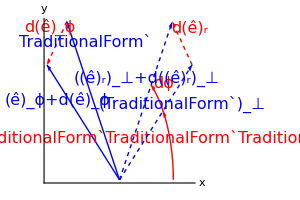

```mathematica
fontsize=16;
{θ1,θ2}={0.2,0.3}π; 
Graphics[{Red,{Dashing[{0.01,0.01}],
          Arrow[{0.5{Cos[θ1],Sin[θ1]},0.5{Cos[θ2],Sin[θ2]}}],Text[Style[fBox["dTraditionalForm`"],fontsize],0.55{Cos[(θ1+θ2)/2],Sin[(θ1+θ2)/2]}],
            Arrow[{0.5{Cos[θ1+π/2],Sin[θ1+π/2]},0.5{Cos[θ2+π/2],Sin[θ2+π/2]}}],Text[Style[fBox["dTraditionalForm`"],fontsize],0.55{Cos[(θ1+θ2)/2+π/2],Sin[(θ1+θ2)/2+π/2]}]},
Circle[{0,0},0.3,{0,θ1}],Arrow[{0.3{Cos[0.99θ1],Sin[0.99θ1]},0.3{Cos[θ1],Sin[θ1]}}],Text[Style["TraditionalForm`TraditionalForm`TraditionalForm`ϕ\ ",fontsize],0.35{Cos[θ1/2],Sin[θ1/2]}],
Circle[{0,0},0.3,{θ1,θ2}],Arrow[{0.3{Cos[0.99θ2],Sin[0.99θ2]},0.3{Cos[θ2],Sin[θ2]}}],Text[Style[fBox["dTraditionalForm`TraditionalForm`TraditionalForm`ϕ"],fontsize],0.35{Cos[(θ1+θ2)/2],Sin[(θ1+θ2)/2]}],
Blue,{Dashing[{0.01,0.01}],Arrow[{{0,0},0.5{Cos[θ1],Sin[θ1]}}],Text[Style["(TraditionalForm`)_⊥",fontsize],0.4{Cos[0.8 θ1],Sin[0.8θ1]}],
Arrow[{{0,0},0.5{Cos[θ2],Sin[θ2]}}],Text[Style[fBox["(TraditionalForm`)_⊥+d(TraditionalForm`)_⊥"],fontsize],0.3{Cos[1.1 θ2],Sin[1.1 θ2]},{0,0},{Cos[ θ2],Sin[ θ2]}]},
Arrow[{{0,0},0.5{Cos[θ1+π/2],Sin[θ1+π/2]}}],Text[Style["TraditionalForm`",fontsize],0.4{Cos[0.8 θ1+π/2],Sin[0.8θ1+π/2]}],
Arrow[{{0,0},0.5{Cos[θ2+π/2],Sin[θ2+π/2]}}],Text[Style[fBox["TraditionalForm`+dTraditionalForm`"],fontsize],0.4{Cos[1.1 θ2+π/2],Sin[1.1 θ2+π/2]},{0,0},{Cos[θ2-π/2],Sin[ θ2-π/2]}]},
Axes -> True ,Ticks -> None, AxesLabel -> {fBox["x"],fBox["y"]},
AxesStyle->fontsize,
PlotRange -> Automatic,ImageSize->300,
AspectRatio->Automatic]
```

Now draw the projection of (ê)_θ on the x–y  plane, and explain what the components are along the two perpendicular directions.

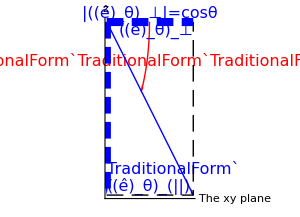

```mathematica
fontsize=16;
{θ1,θ2}={0.2,0.3}π;
eθcoord=0.5{Cos[θ2-π/2],Sin[θ2-π/2]};
Graphics[{  Arrowheads[{0.08}],Red,
Circle[{0,0},0.2,{0,θ2-π/2}],Arrow[{0.2{Cos[(θ2-π/2)],Sin[(θ2-π/2)]},0.2{Cos[1.01(θ2-π/2)],Sin[1.01(θ2-π/2)]}}],Text[Style["TraditionalForm`TraditionalForm`TraditionalForm`θ\ ",fontsize],0.22{Cos[(θ2-π/2)/2],Sin[(θ2-π/2)/2]}],
Blue,
Arrow[{{0,0},eθcoord}],Text[Style["TraditionalForm`",fontsize],0.4{Cos[0.95θ2-π/2],Sin[0.95θ2-π/2]}],
Black,Dashing[{0.04,0.02}],
Line[{{0,eθcoord_⟦2⟧},eθcoord,{eθcoord_⟦1⟧,0}}],Blue,Thickness[0.02],
Arrow[{{0,0},{eθcoord_⟦1⟧,0}}],
Text[Style[fBox["(TraditionalForm`)_⊥"],fontsize],{eθcoord_⟦1⟧,0},{1,1.2}],
Text[Style[fBox["|(TraditionalForm`)_⊥|=cosθ"],fontsize],0.5{eθcoord_⟦1⟧,0},{0,-1.3}],
Arrow[{{0,0},{0,eθcoord_⟦2⟧}}],
Text[Style[fBox["(TraditionalForm`)_(||)"],fontsize],{0,eθcoord_⟦2⟧},{-1.3,-1}]},
Axes -> True ,Ticks -> None, AxesLabel -> {fBox["The xy plane"],fBox["z"]},
AxesStyle->fontsize,
PlotRange -> Automatic,ImageSize->300,
AspectRatio->Automatic]
```

When ϕ changes, draw a picture in the x-y plane to see how ((ê)_θ)_(||) and ((ê)_θ)_⊥  change.

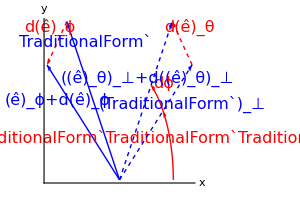

```mathematica
fontsize=16;
{θ1,θ2}={0.2,0.3}π; 
Graphics[{Red,{Dashing[{0.01,0.01}],
          Arrow[{0.5{Cos[θ1],Sin[θ1]},0.5{Cos[θ2],Sin[θ2]}}],Text[Style[fBox["dTraditionalForm`"],fontsize],0.55{Cos[(θ1+θ2)/2],Sin[(θ1+θ2)/2]}],
            Arrow[{0.5{Cos[θ1+π/2],Sin[θ1+π/2]},0.5{Cos[θ2+π/2],Sin[θ2+π/2]}}],Text[Style[fBox["dTraditionalForm`"],fontsize],0.55{Cos[(θ1+θ2)/2+π/2],Sin[(θ1+θ2)/2+π/2]}]},
Circle[{0,0},0.3,{0,θ1}],Arrow[{0.3{Cos[0.99θ1],Sin[0.99θ1]},0.3{Cos[θ1],Sin[θ1]}}],Text[Style["TraditionalForm`TraditionalForm`TraditionalForm`ϕ\ ",fontsize],0.35{Cos[θ1/2],Sin[θ1/2]}],
Circle[{0,0},0.3,{θ1,θ2}],Arrow[{0.3{Cos[0.99θ2],Sin[0.99θ2]},0.3{Cos[θ2],Sin[θ2]}}],Text[Style[fBox["dTraditionalForm`TraditionalForm`TraditionalForm`ϕ"],fontsize],0.35{Cos[(θ1+θ2)/2],Sin[(θ1+θ2)/2]}],
Blue,{Dashing[{0.01,0.01}],Arrow[{{0,0},0.5{Cos[θ1],Sin[θ1]}}],Text[Style["(TraditionalForm`)_⊥",fontsize],0.4{Cos[0.8 θ1],Sin[0.8θ1]}],
Arrow[{{0,0},0.5{Cos[θ2],Sin[θ2]}}],Text[Style[fBox["(TraditionalForm`)_⊥+d(TraditionalForm`)_⊥"],fontsize],0.3{Cos[1.1 θ2],Sin[1.1 θ2]},{0,0},{Cos[ θ2],Sin[ θ2]}]},
Arrow[{{0,0},0.5{Cos[θ1+π/2],Sin[θ1+π/2]}}],Text[Style["TraditionalForm`",fontsize],0.4{Cos[0.8 θ1+π/2],Sin[0.8θ1+π/2]}],
Arrow[{{0,0},0.5{Cos[θ2+π/2],Sin[θ2+π/2]}}],Text[Style[fBox["TraditionalForm`+dTraditionalForm`"],fontsize],0.4{Cos[1.1 θ2+π/2],Sin[1.1 θ2+π/2]},{0,0},{Cos[θ2-π/2],Sin[ θ2-π/2]}]},
Axes -> True ,Ticks -> None, AxesLabel -> {fBox["x"],fBox["y"]},
AxesStyle->fontsize,
PlotRange -> Automatic,ImageSize->300,
AspectRatio->Automatic]
```

Similar figures are drawn in Appendix F.

You can use these results for the rates of change of the unit vectors to find the velocity, and then from the velocity you can find the acceleration.

## Angular velocity

### Instantaneous axis of rotation

A particle moving in space may be considered in any infinitesimal time interval to be moving along an infinitesimal arc of a circle of some suitable radius and center that lies tangent to the actual trajectory at that instant.  Let the x–y plane be the plane of this circle and the origin be its center.  Then, we can use the polar coordinates of Section 1.9.1 for motion in a circle of radius R,

v⃗ =Ṙ  (ê)_r+ R  θ̇ (ê)_θ  =R θ̇(ê)_θ  ,

since the radial component is zero.  We call the line passing through the center of the circle and perpendicular to its plane the instantaneous axis of rotation.  The rate of change θ̇is called the angular speed,

ω = d/dt θ =  θ̇  .

It is useful to make ω into a vector ω⃗, called the angular velocity, by associating a direction with it.  We do this by choosing the direction of the vector ω⃗ along the instantaneous axis of rotation in a right-hand sense, so that the velocity is given by

v⃗ = ω⃗ × r⃗      .

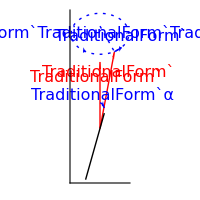

```mathematica
fontsize=16;
Graphics[{Red,Arrow[{{0,0},{1,1.5}}],
Text[Style["TraditionalForm`",fontsize],{0.6,1.1}], 
 {Thick,Arrow[{{0,0},{0,1.3}}]},
Text[Style["TraditionalForm`",fontsize],{-0.25,1}],
    Black,Line[{{0.3,0.3},{-1,-1}}],
Blue,{ Dashing[{0.01,0.02}],Line[{{0,2},{1,1.5}}],Circle[{0,1.85},{2,0.4}]},
Text[Style["TraditionalForm`α",fontsize],{0.19,0.65}],
Arrow[{{-1.1,1.52},{-1,1.5}}],
Circle[{0,0},0.5,π {0.3,0.5}],Arrow[{0.5{Cos[0.31π],Sin[0.31π]},0.5{Cos[0.3π],Sin[0.3π]}}],
Arrow[{{1,1.5},{1.5,1.58}}],
Text[Style["TraditionalForm`",fontsize],{1.48,1.8}],
Text[Style["TraditionalForm`TraditionalForm`TraditionalForm`R",fontsize],{0.65,1.85}]},
Axes -> True ,Ticks -> None, AxesLabel -> None,PlotRange -> Automatic,ImageSize->200,
AspectRatio->Automatic]
```

─────────────────────────────────────────────────────────────────
* * * Lecture 8— 12 September 2019 * * *

### Infinitesimal rotations

What is the connection of vectors with rotations?  We recall that rotations do not necessarily commute, so we may  have λ^(A) λ^(B)≠ λ^(B) λ^(A).  However, vector addition satisfies A⃗ + B⃗ = B⃗ + A⃗ so vectors cannot describe finite rotations.  However, we will see that finite rotations can be made up of products of infinitesimal rotations, and infinitesimal rotations do commute.

An infinitesimal rotation δθ⃗ is a rotation be an angle δθ → 0 in the plane normal to θ⃗ in the right hand sense.

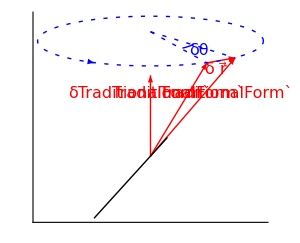

```mathematica
fontsize=16;
Graphics[{Red,Arrow[{{0,0},{1,1.5}}],Text[Style["TraditionalForm`",fontsize],{0.5,1}],
Arrow[{{0,0},{1.5,1.58}}],Text[Style["TraditionalForm`",fontsize],{1.35,1}], 
Arrow[{{1,1.5},{1.5,1.58}}],
Text[Style[fBox["δTraditionalForm`"],fontsize],{1.15,1.4}],
 {Thick,Arrow[{{0,0},{0,1.3}}]},
Text[Style["δTraditionalForm`",fontsize],{-0.2,1}],
    Black,Line[{{0.3,0.3},{-1,-1}}],
Blue,{ Dashing[{0.01,0.02}],Line[{{0,2},{1,1.5}}],Line[{{0,2},{1.5,1.58}}],
Circle[{0,1.85},{2,0.4}]},Arrow[{{-1.1,1.52},{-1,1.5}}],Text[Style[fBox["δTraditionalForm`TraditionalForm`TraditionalForm`θ"],fontsize],{0.85,1.7}],
Circle[{0,1.85},0.4{2,0.4},π {-0.25,-0.1}]},
Axes -> True ,Ticks -> None, AxesLabel -> None,PlotRange -> Automatic,ImageSize->300,
AspectRatio->Automatic]
```

This rotation displaces a point from r⃗ to r⃗  + δ r⃗ where

δ r⃗ = δ θ⃗ × r⃗

Now, try two successive infinitesimal rotations δ(θ⃗)_1 and δ(θ⃗)_2 about different axes.  The position vector r⃗ changes according to

r⃗ →  r⃗ + δ(r⃗)_1  →   r⃗ + δ(r⃗)_1 + δ(r⃗)_2  .

Here,

r⃗ + δ(r⃗)_1 + δ(r⃗)_2 =  r⃗ + δ(θ⃗)_1 × r⃗   + δ(θ⃗)_2× ( r⃗ + δ(r⃗)_1 )  
                                            =  r⃗ + δ(θ⃗)_1 × r⃗   + δ(θ⃗)_2×  r⃗ + δ(θ⃗)_2×δ (r⃗)_1  
                                            ≃  r⃗ + δ(θ⃗)_1 × r⃗   + δ(θ⃗)_2×  r⃗

where we have neglected the product of two infinitesimals.

But, this is equal to

r⃗ + δ(r⃗)_2 + δ(r⃗)_1 =  r⃗ + δ(θ⃗)_2 × r⃗   + δ(θ⃗)_1× ( r⃗ + δ(r⃗)_1 )  
                                            =  r⃗ + δ(θ⃗)_2 × r⃗   + δ(θ⃗)_1×  r⃗ + δ(θ⃗)_1×δ (r⃗)_1  
                                            ≃  r⃗ + δ(θ⃗)_2 × r⃗   + δ(θ⃗)_1×  r⃗      ,

which is the same result.

Thus, infinitesimal rotations can be represented by vectors.  (They are actually axial vectors or pseudovectors.)

## Gradient operator

### The gradient operator ∇

The gradient operator in rectangular coordinates is

∇ = ∑_i (ê)_i  ∂/(∂x_i)

The gradient of the function φ(r⃗) can be written in two ways,

grad φ ≡ ∇φ          .

Acts on a scalar.

Produces a vector.

Direction is that of steepest slope (steepest ascent).

Magnitude is that slope.

The function φ(r⃗) is a scalar, often referred to as a scalar field.  In rectangular coordinates,

∇=x̂ ∂/(∂x)+ŷ ∂/(∂y)+ẑ ∂/(∂z).

### The gradient of a scalar is a vector

The gradient of a scalar φ(r⃗) is a vector if, under a cordinate transformation, its components (∂φ(x ))/(∂x_i) transform like the components A_i of a vector A⃗,

A_i' = ∑_j λ_ij A_j     ,

while φ' = φ is unchanged because it is a scalar (Section 1.7).

The chain rule gives us

(∂φ'(x' ))/(∂x_i') =  ∑_j ( (∂x_j)/(∂x_i') ) ( (∂φ(x ))/(∂x_j) )   .

The coordinates transform as

x_i' = ∑_j λ_ij x_j     ,

with inverse transformation

x_i = ∑_j [ λ^-1]_ij x_j'     .

This last relation allows us to see that the partial derivatives of the old coordinates with respect to the new ones are

(∂x_i)/(∂x_j') = [ λ^-1]_ij   ,

the matrix elenents of the inverse λ^-1.  Our rotation matrices that we use to illustrate coordinate transformations are orthogonal matrices, and in that case we may write (note that I have sneakily transposed indices to get the derivative I wanted above)

(∂x_j)/(∂x_i') = [ λ^-1]_ji =  [ λ^t]_ji = λ_ij   .

We see that the matrix elements of the orthogonal transformation matrix λ are given by (∂x_j)/(∂x_i') = λ_ij, which we can use in

(∂φ'(x' ))/(∂x_i') =  ∑_j ( (∂x_j)/(∂x_i') ) ( (∂φ(x ))/(∂x_j) ) =   ∑_j λ_ij ( (∂φ(x ))/(∂x_j) )        .

Thus, the components (∂φ(x ))/(∂x_i) of ∇φ transform under our orthogonal transformations as a vector, and as a consequence the gradient of a scalar is a vector.

You will learn in later life that, although all this is correct for orthogonal transformations, I have oversimplified the situation by sticking to that example.  Nevertheless, the conclusion that the gradient of a scalar transforms as a vector is correct.

### The direction of steepest ascent

To illustrate the meaning of the gradient, look at an  inverted-bowl-shaped hill in two dimensions.

```mathematica
fontsize=16;
Show[{Plot3D[-(x^2+ y^2), {x,-1,1},{y,-1,1}, AxesLabel -> {fBox["x"],fBox["y"]},
AxesStyle->16,
 Ticks -> None, RegionFunction -> (#1^2+#2^2 ≤ 0.5&), Mesh -> None],
ParametricPlot3D[{0,y,- y^2}, {y,-1,0}, AxesLabel -> {fBox["x"],fBox["y"]},
AxesStyle->16, Ticks -> Automatic,PlotStyle -> {Thick,Blue}]}]
```

-Graphics3D-

Here is a contour map of the hill with two contours φ and φ + dφ indicated.

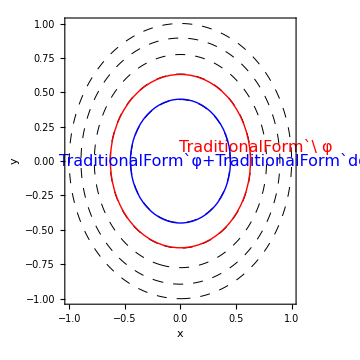

```mathematica
fontsize=16;ContourPlot[ -(x^2+ y^2), {x,-1,1},{y,-1,1}, FrameLabel -> {fBox["x"],fBox["y"]}, 
FrameStyle->fontsize,
ContourShading -> None, 
Contours -> Range[-1,0,1/5], ContourStyle ->{ {Dashing[{0.02,0.02}],Thickness[0.002]}},
PlotPoints -> 50, ImageSize->Medium,
Epilog -> MapThread[ {#1,Circle[{0,0},#2],Text[Style[#3,fontsize],#4]} &, 
                      {{Red,Blue},1/5{3.15,2.25},{"TraditionalForm`\ φ","TraditionalForm`φ+TraditionalForm`dφ"},{{0.68,0.1},{0.3,0}}}] ]
```

Pick two contours separated by a fixed height dφ.  Write

dφ = (∂φ)/(∂x) dx  + (∂φ)/(∂y) dy = ( ∇φ  ) · d r⃗

where d r⃗ = x̂ dx + ŷ dy.  Write this as

dφ = | ∇φ  |  | d r⃗ | cos θ.

What angle makes   | d r⃗ | = dφ/(| ∇φ |   cos θ) shortest?  Answer: θ=0.  The shortest distance | d r⃗ | is that of steepest ascent, and is parallel to ∇φ.

The directional derivative of φ in the n̂ direction is n̂ · ∇φ.

─────────────────────────────────────────────────────────────────
* * * Lecture 9— 17 September 2019 * * *

## Divergence

The divergence of  V⃗(r⃗) can be written in two ways,

div V⃗ ≡ ∇ · V⃗        .

Acts on a vector.

Produces a scalar.

Gives the outflow (per unit volume).

The function V⃗(r⃗) is a vector, often referred to as a vector field.

To illustrate the meaning of the divergence, consider ∇ · (ρ v⃗ ) for a compressible fluid of density ρ and velocity v⃗(r⃗).  If we look at an infinitesimal rectangular parallelopiped of sides dx, dy, and dz, we can calculate the flow in through each of its sides.

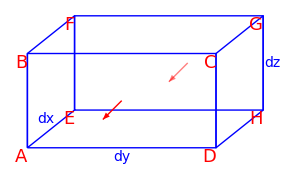

```mathematica
Graphics[v=Flatten[Outer[#1+#2&,{{0,0},{0.5,0.4}},{{0,0},{0,1},{2,1},{2,0}},1,1],1];
{GraphicsComplex[v,{Blue,Thick,Line[{1,2,3,4,1}] ,Line[{5,6,7,8,5}],Line[{1,2,6,5,1}],Line[{3,4,8,7,3}],
MapThread[Text[Style[#1,18,Red,Background->White],#2,{1,1}]&,{{"A","B","C","D","E","F","G","H"},{1,2,3,4,5,6,7,8}}]} ],
  Text[Style[fBox["dx"],14,Blue],{0.2,0.3}],Text[Style[fBox["dy"],14,Blue],{1,-0.1}],Text[Style[fBox["dz"],14,Blue],{2.6,0.9}],
Red, Arrow[{{1,0.5},{0.8,0.3}}],Opacity[0.5],Arrow[{{1.7,0.9},{1.5,0.7}}]},
ImageSize -> 300]
```

The flow tangent to a face contributes nothing, and so we find, for the back face located at x=0,

[rate of flow in]_EFGH = [ρ v_x]_(x=0) dy  dz  .

For the front face located at x=dx,

[rate of flow out]_ABCD =( [ρ v_x]_0 + dx  ∂/(∂x) (ρ v_x)  )  dy  dz  .

The net result is

[net rate of flow out]_(x direction) = [∂/(∂x) (ρ v_x) ]_0  dx   dy  dz  .

We have similar expressions for the other two directions, and, adding them together,

net rate of flow out per unit time = [∂/(∂x) (ρ v_x) + ∂/(∂y) (ρ v_y)  + ∂/(∂z) (ρ v_z)  ]  dx   dy  dz 
                                                                           =  [ ∇ · (ρ v⃗)  ]  dx   dy  dz         .

You likely see the origin of the name "divergence" of the flow.  As an added benefit, we see that this expression gives

(∂ρ)/dt + ∇ · (ρ v⃗) =0,

which is the continuity equation.  It is a result of the conservation of mass (or molecules) of the fluid.  We will use a similar continuity equation for electric charge and current, which is a consequence of the conservation of electric charge.

## Laplacian

The Laplacian is

∇ · ∇ ≡ ∇^2= ∑_i ∂^2/(∂x_i^2)       ,

where the third form refers specifically to rectangular coordinates.  In other coordinate systems the expression is more complicated, and you have to look it up in Appendix F.  The Laplacian

gives, geometrically, a measure of curvature.

can act either on a scalar or a vector field, and does not change its character.

You saw examples of these operations in Homework Problem 2.3 (Thornton and Marion, fifth edition,  problem 1.31),

∇ r^n = (ê)_r ∂/(∂r) r^n =  (ê)_r n  r^(n-1) = n  r^(n-2) r⃗   ,

and

∇^2 ln r = 1/r^2 ∂/(∂r) r^2 ∂/(∂r) ln r =  1/r^2 ∂/(∂r) r^2 1/r=1/r^2   .

## Curl

The curl of  V⃗(r⃗) can be written in two ways,

curl V⃗ ≡ ∇ × V⃗        .

Acts on a vector.

Produces a vector.

Gives the circulation (per unit area).

The function F⃗(r⃗) is a vector, often referred to as a vector field.  In rectangular coordinates,

∇ × V⃗ = x̂ (∂/(∂y)V_z-∂/(∂z)V_y) +  ŷ (∂/(∂z)V_x-∂/(∂x)V_z) +  ẑ (∂/(∂x)V_y-∂/(∂y)V_x)
                                 =  |x̂  | ŷ  | ẑ 
∂/(∂x) | ∂/(∂y) | ∂/(∂z)
V_x | V_y | V_z|              .

To illustrate the meaning of the curl, consider the circulation of a fluid around a rectangular loop in the x – y plane.  The circulation of a vector field V⃗ around a closed contour C is the line integral ∫_C  dℓ⃗  · V⃗, and we will picture V⃗(r⃗) as the velocity of the fluid.  (I write d ℓ⃗  for a line element here.)  If we let the contour be an infinitesimal rectangular loop of sides dx and dy, it is easy to calculate the circulation.

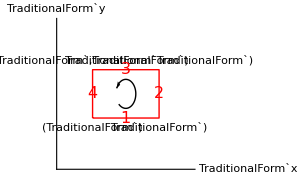

```mathematica
fontsize=16;fontsize1=
Graphics[{Red,
Line[Map[#+{1,1}&,{{0,0},{2,0},{2,1},{0,1},{0,0}}]],
    Black,MapThread[ Text[Style[#1,"Text",Italic,FontFamily->"Times"],#2,
FormatType->TraditionalForm] &, 
{{"(TraditionalForm`)","TraditionalForm`)","TraditionalForm`TraditionalForm`)","TraditionalForm`,TraditionalForm`)"},Map[#+{1,1}&,{{0,-0.2},{2,-0.2},{2,1.2},{0,1.2}}]} ], 
MapThread[ Text[Style[#1,Red,fontsize,Background->White],#2] &, {{"1","2","3","4"},
Map[#+{1,1}&,{{1,0},{2,0.5},{1,1},{0,0.5}}]}],
                          Circle[{2,1.5},0.3,{-(3π)/4,(3π)/4 }],{Black,
Arrow[{{2,1.5} + 0.3{Cos[(3π)/4],Sin[(3π)/4]},{2,1.5} + 0.3{Cos[(7π)/8],Sin[(7π)/8]}}]}},
 Axes ->True, AxesLabel-> {"TraditionalForm`x","TraditionalForm`y"},
AxesStyle->16,
 PlotRange -> {{0,4},{0,3}}, Ticks -> None,ImageSize->300,AspectRatio->1/GoldenRatio]
```

The circulation around the four sides of the rectangle is

[circulation]_1234 = ∫_1  d ℓ_x  V_x + ∫_2  d ℓ_y  V_y + ∫_3  d ℓ_x  V_x + ∫_4  d ℓ_y  V_y  .

Because the loop is infinitesimal, we can take the velocity as effectively constant along each side.  Then,

∫_1  d ℓ_x  V_x= V_x(x_0,y_0) dx   ,  
          ∫_2  d ℓ_y  V_y= V_y(x_0+ dx,y_0) dy = [ V_y(x_0,y_0) + (∂V_y(x_0,y_0))/(∂x) dx ]  dy  , 
          ∫_3  d ℓ_x  V_x=  V_x(x_0,y_0+  dy ) (- dx ) = -   [ V_y(x_0,y_0) + (∂V_x(x_0,y_0))/(∂y) dy ]  dx  ,
          ∫_4  d ℓ_y  V_y=  V_y(x_0,y_0 ) (- dy )  .

The contributions involving V_x(x_0,y_0)  and V_y(x_0,y_0)  all cancel, and we are left with

[circulation]_1234 = ( (∂V_y)/(∂x) -(∂V_x)/(∂y)) dx  dy  .

Dividing by  dx  dy gives

circulation per unit area = ( (∂V_y)/(∂x) -(∂V_x)/(∂y))  = ẑ · ∇ × V⃗  .

## Integration of vectors

### Line integral

The line integral of a vector field A⃗(s) along a curve from point P to point Q is

∫_P^Q A⃗ · d s⃗  =  ∑_i ∫_P^Q A_i · d s_i

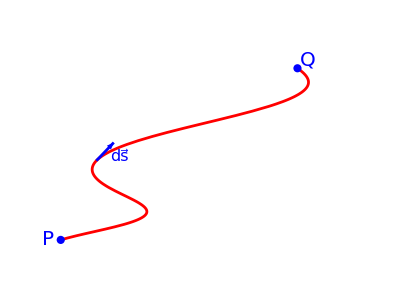

```mathematica
path[t_]:={(t+Sin[3t])^2,(t )^2}
ds[t_]:={2(t+Sin[3t])(1+3Cos[3t]),2t}
force=7{Cos[(5π)/8],Sin[(5π)/8]};
t1=2;
t2=5;
tp=3.7;
ptRadius=0.5;
rangeForPlot={{0,40},{0,30}};
labels={Blue,Disk[path[t1],ptRadius],Disk[path[t2],ptRadius],Thickness[0.005],
Arrow[{path[tp],path[tp]+0.3ds[tp]}],
Text[Style[fBox["ds⃗"],16],path[tp]+0.4ds[tp]+{0,-2.5}],
Blue,Text[Style["P",{20}],path[t1]-{1.5,0}],
Text[Style["Q",{20}],path[t2]+{1.2,1}]};
pathPlot=ParametricPlot[path[t],{t,t1,t2},AxesOrigin->{0,0},
PlotRange->rangeForPlot,PlotStyle->{Red,Thickness[0.005]},ImageSize->400,Axes->False,Epilog->{labels}]
```

The line integral of a gradient just gives the values of the scalar field at the endpoints,

∫_P^Q  ds⃗  · ∇φ =  ∑_i ∫_P^Q  d s_i ∂/(∂x_i) φ = φ(Q) - φ(P)  .

This is simply the three-dimensional version of

∫_p^q dx d/dx f(x) = f(q) - f(p)     .

### Surface integral

The surface integral of a vector field A⃗(r⃗) over a surface S is

∫_S  A⃗ · d a⃗  =  ∫_S (  A⃗ · n̂ )  da        .

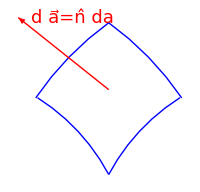

```mathematica
Graphics[{Blue,Thick,MapThread[Circle[#1,#2,#3 ]&,{{{-1,0},{-1,0},{1,0},{1,0}},
{0.8 √2{1,1},1.2 √2{1,1},0.8 √2{1,1},1.2 √2{1,1}},{π{0.155,0.32},π{0.19,0.3},π{0.68,0.845},π{0.7,0.81}}}],
    Text[Style[fBox["da⃗=n̂da"],18,Red],{-0.2,1.4}],Red, Arrowheads[Large],Arrow[{{0,1},{-0.5,1.4}}]},
ImageSize -> 200]
```

Here, the area element is

d a⃗  =  n̂   da

where  n̂  is an outward normal to the surface.  In rectangular coordinates da might be dx  dy and d a⃗ = ẑ d  dy.  The surface integral is a dot product, and the result is a scalar.

### Volume integral

The volume intergral of a vector field A⃗(r⃗) over a volume V is

∫_V d V A⃗(r⃗) = ∫_V d V ∑_i  (ê)_i A_i( r⃗ )  = ∫_V d V ∑_i  (ê)_i A_i( r⃗ )   .

In rectangular coordinates this is

∫_V d V A⃗(r⃗) = ∫_V d V  (  x̂ A_x( r⃗ )  +   ŷ  A_y( r⃗ )   +   ẑ  A_z( r⃗ )   ) 
                        =  x̂  ∫_V d VA_x( r⃗ )  +   ŷ  ∫_V d V A_y( r⃗ )   +   ẑ  ∫_V d V A_z( r⃗ )

where

dV = dx  dy  dz  .

That is, you just  integrate each component separately.  If you divide by the total volume V, this just produces the volume average of each component.  This is about the only direct use I've found for this volume integral.

─────────────────────────────────────────────────────────────────
* * * Lecture 10— 19 September 2019 * * *

## Divergence theorem

The divergence theorem is

∫_(Volume Ω) d^3 r  ∇ · V⃗( r⃗ ) = ∫_(Surface S) d^2 r   n̂ · V⃗  .

where Ω is the volume and S is its surface, and n̂ is a unit vector normal to the surface S at each point.  I write d^3 r for a volume element and d^2 r for an area element.  You can write dV or dv and dA or da if you prefer, as long as you are not using these letters for something else.)

The proof is as follows.  Divide the volume into infinitesimal cubes like those in our discussion of the fluid flow in Section 1.2.  As we showed there, for each cube,

∑_(six surfaces) ( n̂ · V⃗) d^2 r = ( ∇ · V⃗)  d^3 r  .

Now, some of these surfaces are interior, while some are exterior and part of the surface S.  At interior surfaces, what flows out of one flows into a neighboring cube, and so these contributions cancel.  Thus,

∑_(all cubes) ( ∇ · V⃗)  d^3 r = ∑_(all cubes) ∑_(six surfaces) ( n̂ · V⃗) d^2 r
                                                            = ∑_(exterior surfaces) ( n̂ · V⃗) d^2 r           .

Replacing sums by integrals gives the divergence theorem.  The divergence theorem is usually called Gauss's theorem by Thornton and Marion.

## Stokes's theorem

Stokes's theorem is

∫_(Surface S) d^2 r   n̂ ·  ∇ × V⃗( r⃗ ) = ∮_(Curve C) dℓ⃗  · V⃗( r⃗ )    ,

where S is a surface, C is the curve around its edge (its perimeter), and n̂ is the normal to S in a right-hand sense of going around C.

To prove Stokes's theorem, divide the surface into infinitesimal rectangles as in Section 1.5 above.  For each rectangle, we found there that

∑_(four sides) V⃗ ·  d ℓ⃗  = n̂ · ∇ × V⃗  d^2 r  .

Now, some of these edges are interior, while some are exterior and part of the curve C.  At interior edges, the flows cancel.  Thus,

∑_(all rectangles) ( ∑_(four sides) V⃗ ·  d ℓ⃗  ) = ∑_(all rectangles) n̂ · ∇ × V⃗  d^2 r  .

Replacing sums by integrals gives Stokes's theorem.

Notice that Stokes's theorem as we have written it applies to an open surface.  We can regard a closed surface as a limiting case where the perimeter shrinks to zero.  Then, the line integral on the left is zero.

Here is a picture of an open surface S with a red contour C around the perimeter.

```mathematica
Show[{Plot3D[-(x^2+ y^2), {x,-1,1},{y,-1,1},  Axes -> None, Ticks -> None, RegionFunction -> (#1^2+#2^2 ≤ 0.5&), Mesh -> None, Boxed -> False],ParametricPlot3D[{Cos[θ]/(√2),Sin[θ]/(√2),-1/2}, {θ,0,2π}, AxesLabel -> {"x","y"}, Ticks -> Automatic,PlotStyle -> {Thick,Red}],
Graphics3D[{Text[Style["Contour C",Red,18],{1.1,0,-0.1}],Red,Line[{{1/(√2),0,-0.5},{1,0,-0.2}}],
Text[Style["Surface S",Blue,18],{-0.5,0,-0.}],Blue,Line[{{0,0,-0.5},{-0.5,0,-0.05}}]}]}]
```

-Graphics3D-